◼"◼"◼"◼"2023-11-20v2.00◼"◼"M. J. Steil[msteil@theorie.ikp.physik.tu-darmstadt.de](mailto:msteil@theorie.ikp.physik.tu-darmstadt.de)TU Darmstadt

# Zero dimensional O(N=1) model

Martin Jakob Steil^1

^1Technische Universität Darmstadt

https://arxiv.org/abs/2108.10085
Computed trajectories “SC*.mx.gz” are available upon request (msteil@theorie.ikp.physik.tu-darmstadt.de)

Initialization

Print[DateString["ISODateTime"]];
LaunchKernels[20];
Print["$KernelCount=",$KernelCount];

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

#### Git setup

[https://mathematica.stackexchange.com/questions/11258/are-there-suitable-versioning-systems-for-mathematica-notebooks, 2019.02.12 12:01]

```mathematica
(* Disable Notebookhistory *)
SetOptions[InputNotebook[],PrivateNotebookOptions->{"FileOutlineCache"->False},TrackCellChangeTimes->False]
```

#### Packages

```mathematica
<<CompiledFunctionTools` (* For CompilePrint[] *)

(* Provides RGB or CMYK (if GUCD`GUCDuseCMYK=True) colors form the corporate design of Goethe university. Use GUCD`showAll[] to see all colors. *)
GUCD`useCMYK=True;
Get["D:/Github/Mathematica/Packages/CorporateDesigns/GUCD.m"];
```

#### Notebook style

```mathematica
Legend[exp_,pos_:{Right,Top}]:=Placed[Style[#,FontFamily->"Helvetica",FontSize->12,SingleLetterItalics->True]&/@exp,pos]
LabelText[txt_]:=Text[txt,BaseStyle->{FontFamily->"Helvetica",FontSize->11}]
ListLineListPlot[dat_,opt___]:=Show[{ListPlot[dat,opt],ListLinePlot[dat]}]

xDot[r_,thick___:1]:=Graphics[{AbsoluteThickness[thick],Line[{{1,1},{-1,-1}}],Line[{{-1,1},{1,-1}}]},ImageSize->r,AlignmentPoint->{0,0}]
outputStyle[exp_]:=Style[exp//TraditionalForm,Blue]
fixTickThickness[gr_]:=gr/.f:(_Charting`ScaledTicks|_Charting`ScaledFrameTicks):>(Part[#,;;, ;;3]&@*f)

Plot`Style`Beamer={BaseStyle->{FontFamily->"Helvetica",FontSize->12},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],Axes->False};

Plot`Style=Plot`Style`Beamer;
SetOptions[Plot,Plot`Style];
SetOptions[ListPlot,Plot`Style];
SetOptions[RegionPlot,Plot`Style];
SetOptions[ListLinePlot,Plot`Style];
```

#### Methods

```mathematica
(* Modified Version of http://szhorvat.net/pelican/save-data-in-notebooks.html *)
SetAttributes[SaveToCell,HoldFirst]
SaveToCell[var_,name:Except[_?OptionQ]:"",opt:OptionsPattern[]]:=With[
{
data=Evaluate[var],
label=name<>If[name!="",", ",""]<>DateString["ISODateTime"]
},
CellPrint@Cell[BoxData@RowBox[{MakeBoxes[var],"=",ToBoxes[Iconize[data,label,Method->Compress]],";"}],"Input",GeneratedCell->False,(*prevent deletion by Cell>Delete All Output:*)CellLabel->"(saved)",opt,CellLabelAutoDelete->False]
]

(** Option lookup **)
LookupOption[x_,option_]:=Lookup[Options[If[Head[x]=!=Symbol,Head[x],x]],option]
LookupOption[x_,option_,default_]:=Lookup[Options[If[Head[x]=!=Symbol,Head[x],x]],option,default]
```

```mathematica
ClearAll[ContextQ];
ContextQ[name_]:=If[Length[Names[ToString[name]<>"`*"]]==0,False,True]
ContextQ::usage="ContextQ[name_]: Return True if name is a context (has sub expressions 'name`...').";

ClearAll[GetSubContexts];
Options[GetSubContexts]={
	Depth->10
};
GetSubContexts[name_]:=Block[{names=((ToString[name]<>#)&/@Array[StringJoin@@ConstantArray["`*",#]&,LookupOption[GetSubContexts,Depth,10]])},
	StringReplace[Flatten[Names[#]&/@names],RegularExpression["(.*)`(.*[^`])"]->"$1`"]//DeleteDuplicates
]
GetSubContexts::usage="GetSubContexts[name_]: Extract possible sub contexts 'name`*`...' and return '{}' if name is not a context.";

ClearAll[GetDistributedContexts];
GetDistributedContexts[]:=If[ListQ[$DistributedContexts]=!=True,{$Context},$DistributedContexts]
GetDistributedContexts::usage="GetDistributedContexts[]: Return $DistributedContexts if $DistributedContexts is a list and {$Context} if its not a list.";

ClearAll[AddToDistributedContexts];
AddToDistributedContexts[name_String/;StringMatchQ[name,RegularExpression["(.*)`"]]]:=With[{contexts=DeleteDuplicates@Join[{},GetDistributedContexts[],{name}]},$DistributedContexts=contexts;Return[contexts]]
AddToDistributedContexts[names_/;VectorQ[names,If[StringQ[#],StringMatchQ[#,RegularExpression["(.*)`"]],False]&]]:=With[{contexts=DeleteDuplicates@Join[{},GetDistributedContexts[],names]},$DistributedContexts=contexts;Return[contexts]]

AddToDistributedContexts[names_List,includeSubContexts_:True]:=AddToDistributedContexts[#,includeSubContexts]&/@names;
AddToDistributedContexts[name_,includeSubContexts_:True]:=With[{
	contexts=If[includeSubContexts,GetSubContexts[name],If[ContextQ[name],{name},{}]]
},
	
	$DistributedContexts=Join[GetDistributedContexts[],contexts]//DeleteDuplicates;	
	Return[contexts]
]
AddToDistributedContexts::usage="AddToDistributedContexts[name_,OptionsPattern[],includeSubContexts_:True]: Add name to $DistributedContexts if name is a context and include sub contexts if includeSubContexts=True using GetSubContexts[...].";
```

## Kurganov-Tadmor Scheme

### Finite Volume

In the following  1+1 dimensional PDE
∂_t u(t,x)+∂_x F[t,u(t,x)]=∂_x Q[t,x,u(t,x),∂_x u(t,x)]+∂_x S(t,x)+G[t,x,u]

We average over n volume cells on an equidistant grid of n+1 cell boundaries x_j∈[x_(1/2),x_(1+1/2),...,x_(n+1/2)];
∫_(x_(j-1/2))^(x_(j+1/2)) dx/Δx∂_t u(t,x)+∫_(x_(j-1/2))^(x_(j+1/2)) dx/Δx∂_x F[t,u(t,x)]=∫_(x_(j-1/2))^(x_(j+1/2)) dx/Δx∂_x Q[t,x,u(t,x),∂_x u(t,x)]+∫_(x_(j-1/2))^(x_(j+1/2)) dx/Δx∂_x S(t,x)
∂_t u_j+(F[t,u(t,x_(j+1/2))]-F[t,u(t,x_(j-1/2))])/Δx=(Q[t,x_(j+1/2),u(t,x_(j+1/2)),∂_x u(t,x+1/2)]-Q[t,x_(j-1/2),u(t,x_(j-1/2)),∂_x u(t,x-1/2)])/Δx+(S[t,x_(j+1/2)]-S[t,x_(j-1/2)])/Δx
A finite volume scheme specifies how to compute/reconstruct the convection and diffusion flux on the cell boundaries from the available cell averages u_i∈[u_1,...,u_n];
∂_t u_j+(H_(j+1/2)[u]-H_(j-1/2)[u])/Δx=(Q_(j+1/2)[u]-Q_(j-1/2)[u])/Δx+S_j
A cell with average u_j is centered at x_j=x_(j-1/2)+Δx/2

### Limiters

```mathematica
ClearAll["KT`ϕ`*"]
KT`ϕ`MinMod=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,1.,Max[0.,Min[1.,Δuj/Δujp1]]]];
KT`ϕ`VanAlbada1=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,1.,With[{r=Δuj/Δujp1},r(r+1.)/(r*r+1.)]]];
KT`ϕ`VanLeer=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,2.,With[{r=Δuj/Δujp1},(r+Abs[r])/(1+Abs[r])]]];
KT`ϕ`MonotonizedCentral=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,2.,With[{r=Δuj/Δujp1},Max[0.,Min[2r,0.5*(1+r),2.]]]]];
KT`ϕ`Koren=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,2.,With[{r=Δuj/Δujp1},Max[0.,Min[2r,Min[(1.+2.*r)/3.,2.]]]]]];
KT`ϕ`Superbee=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,2.,With[{r=Δuj/Δujp1},Max[0.,Min[2.r,1.],Min[r,2.]]]]];

KT`ϕ`VanAlbada2=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,0.,With[{r=Δuj/Δujp1},2.*r/(r*r+1.)]]](* Not TVD *);
```

Plots

```mathematica
KT`TVDregion=Show[{RegionPlot[(ϕ<=2r&&ϕ>=r&&ϕ≤1)||(r>=1&&ϕ≥1&&ϕ≤2&&ϕ<=r),{r,0,4},{ϕ,0,3},PlotRange->{{0,4},{0,3}},PlotPoints->50,MaxRecursion->4,FrameLabel->{"r","ϕ(r)"},PlotLegends->Legend[{"TVD region"},{Right,Bottom}],PlotStyle->Blend[{White,Black},1/6],BoundaryStyle->None,AspectRatio->3/4],Graphics[{Arrowheads[0.03],Arrow[{{6/4,3/4},{6/4,3/4-1/2}}],Text["   increasing dissipativity",{6/4,3/4-1/4},{-1,0}]}],Graphics[{Arrowheads[0.03],Arrow[{{6/4,2+1/4},{6/4,2+3/4}}],Text["   decreasing dissipativity",{6/4,2+2/4},{-1,0}]}]}];
Show[{KT`TVDregion,Plot[{KT`ϕ`MinMod[r,1],KT`ϕ`VanAlbada1[r,1],KT`ϕ`VanLeer[r,1],KT`ϕ`MonotonizedCentral[r,1],KT`ϕ`Koren[r,1],KT`ϕ`Superbee[r,1],KT`ϕ`VanAlbada2[r,1]},{r,0,4},PlotStyle->AbsoluteThickness[2],PlotRange->All,PlotLegends->Legend[{"MinMod","van Albada 1","van Leer","Monotonized Central","Koren","Superbee","van Albada 2"},{Left,Top}]]},ImageSize->500]//fixTickThickness
```

```mathematica
KT`ϕ`GeneralizedMinMod[θ_]/;1<=θ≤2:=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,θ,With[{r=Δuj/Δujp1},Max[0.,Min[θ r,0.5*(1+r),θ]]]]];
```

```mathematica
Table[{θ,KT`ϕ`GeneralizedMinMod[θ][r,1]},{θ,1,2,1/4}];
Show[{KT`TVDregion,Plot[Evaluate[%[[All,2]]],{r,0,4},PlotStyle->AbsoluteThickness[2],PlotRange->All,PlotLegends->Legend[Row[{Subsuperscript["ϕ","gmm",InputForm@#]}]&/@%[[All,1]],{Left,Top}]]},ImageSize->500]//fixTickThickness
```

### Boundary conditions

```mathematica
BC`periodic=Function[{vin},Module[{v},
v=vin;
v[[All,1]]=v[[All,-5]];(* Subscript[u, -2]= Subscript[u, n-3] *)
v[[All,2]]=v[[All,-4]];(* Subscript[u, -1]= Subscript[u, n-2] *)
v[[All,-3]]=v[[All,3]];(* Subscript[u, n-1]= Subscript[u, 0] *)
v[[All,-2]]=v[[All,4]];(* Subscript[u, n] = Subscript[u, 1] *)
v[[All,-1]]=v[[All,5]];(* Subscript[u, n+1] = Subscript[u, 2] *)
v
]];
```

```mathematica
BC`antiperiodic=Function[{vin},Module[{v},
v=vin;
v[[All,1]]=-v[[All,-5]];(* Subscript[u, -2]= -Subscript[u, n-3] *)
v[[All,2]]=-v[[All,-4]];(* Subscript[u, -1]= -Subscript[u, n-2] *)
v[[All,-3]]=-v[[All,3]];(* Subscript[u, n-1]= -Subscript[u, 0] *)
v[[All,-2]]=-v[[All,4]];(* Subscript[u, n] = -Subscript[u, 1] *)
v[[All,-1]]=-v[[All,5]];(* Subscript[u, n+1] = -Subscript[u, 2] *)
v
]];
```

```mathematica
BC`linearExtrapolation=Function[{vin},Module[{v},
v=vin;
v[[All,1]]=3v[[All,3]]-2v[[All,4]];(* Subscript[u, -2] = 3 Subscript[u, 0] - 2 Subscript[u, 1]*)
v[[All,2]]=2v[[All,3]]-v[[All,4]];(* Subscript[u, -1] = 2 Subscript[u, 0] - Subscript[u, 1]*)
v[[All,-2]]=2v[[All,-3]]-v[[All,-4]];(* Subscript[u, n] = 2 Subscript[u, n-1] - Subscript[u, n-2]*)
v[[All,-1]]=3v[[All,-3]]-2v[[All,-4]];(* Subscript[u, n+1]= 3 Subscript[u, n-1] - 2 Subscript[u, n-2]*)
v
]];
```

```mathematica
BC`antisymmetric=Function[{vin},Module[{v},
v=vin;
v[[All,1]]=-v[[All,5]];(* Subscript[u, -2] = -Subscript[u, 2] *)
v[[All,2]]=-v[[All,4]];(* Subscript[u, -1] = -Subscript[u, 1] *)
v[[All,3]]=0*v[[All,3]]; (* Subscript[u, 0] = 0 *)
v[[All,-2]]=2v[[All,-3]]-v[[All,-4]];(* Subscript[u, n] = 2 Subscript[u, n-1] - Subscript[u, n-2]*)
v[[All,-1]]=3v[[All,-3]]-2v[[All,-4]];(* Subscript[u, n+1]= 3 Subscript[u, n-1] - 2 Subscript[u, n-2]*)
v
]];
```

Symbolic and numeric tests

```mathematica
Table[{u[i,0]},{i,{0,1,2,n-3,n-2,n-1}}]//Transpose//Flatten
BC`periodic[Join[{0.,0.},#,{0.,0.}]&/@Partition[Take[%,{1,6*1}],6]]

5;
Table[x+%,{x,0,2π,π/8}];
BC`periodic[{ArrayPad[Sin[%],2]}];
{#[[3;;-3]],Join[#[[1;;2]],#[[-2;;-1]]]}&@Transpose[{Table[x+%%%,{x,-π/4,2π+π/4,π/8}],%[[1]]}];
Show[{ListPlot[%],Plot[Sin[x],{x,First[Last[%]][[1]],Last[Last[%]][[1]]}]}]
```

```mathematica
Table[{u[i,0]},{i,{0,1,2,n-3,n-2,n-1}}]//Transpose//Flatten
BC`antiperiodic[Join[{0.,0.},#,{0.,0.}]&/@Partition[Take[%,{1,6*1}],6]]

π/4;
Table[x+%,{x,0,π,π/8}];
BC`antiperiodic[{ArrayPad[Sin[%],2]}];
{#[[3;;-3]],Join[#[[1;;2]],#[[-2;;-1]]]}&@Transpose[{Table[x+%%%,{x,-π/4,π+π/4,π/8}],%[[1]]}];
Show[{ListPlot[%],Plot[Sin[x],{x,First[Last[%]][[1]],Last[Last[%]][[1]]}]}]
```

```mathematica
Table[{u[i,0]},{i,{0,1,2,n-3,n-2,n-1}}]//Transpose//Flatten
BC`linearExtrapolation[Join[{0.,0.},#,{0.,0.}]&/@Partition[Take[%,{1,6*1}],6]]

5;
Table[x+%,{x,0,2π,π/8}];
BC`linearExtrapolation[{ArrayPad[Sin[%],2]}];
{#[[3;;-3]],Join[#[[1;;2]],#[[-2;;-1]]]}&@Transpose[{Table[x+%%%,{x,-π/4,2π+π/4,π/8}],%[[1]]}];
Show[{ListPlot[%],Plot[Sin[x],{x,First[Last[%]][[1]],Last[Last[%]][[1]]}]}]
```

```mathematica
Table[{u[i,0]},{i,{0,1,2,n-3,n-2,n-1}}]//Transpose//Flatten
BC`antisymmetric[Join[{0.,0.},#,{0.,0.}]&/@Partition[Take[%,{1,6*1}],6]]

0;
Table[x+%,{x,0,3π/2,π/8}];
BC`antisymmetric[{ArrayPad[Sin[%],2]}];
{#[[3;;-3]],Join[#[[1;;2]],#[[-2;;-1]]]}&@Transpose[{Table[x+%%%,{x,-π/4,3π/2+π/4,π/8}],%[[1]]}];
Show[{ListPlot[%],Plot[Sin[x],{x,First[Last[%]][[1]],Last[Last[%]][[1]]}]}]
```

### System and solution objects

#### System

```mathematica
ClearAll[KT`system`generate];
KT`system`generate[scheme_:KT`O2,schemeParams___][nx`in_,nu`in_:1][x0`in_,x1`in_][t0`in_,t1`in_][F_,λdFdu_,Q_,BC_,pars___][u0`in_,u0`in`pars___][average_:Integrate,averageOptions___]:=Module[
{nx,nu,nadd,
x0,x1,Δx,xi,xi12,
t0,t1,
pde,pde`params,pde`rhs,pde`rhs`function,
u0,U0,u0`pars,u0i,
pde`system,pde`u,pde`t},

(* **** Grid **** *)
nx=nx`in;
nu=nu`in;

x0=x0`in;
x1=x1`in;
Δx=(x1-x0)/(nx-1);
xi=Table[x0+Δx*i,{i,0,nx-1}];
xi12=Table[x0+Δx*(i-0.5),{i,0,nx}];

(* **** PDE **** *)
t0=t0`in;
t1=t1`in;
pde=Sequence[F,λdFdu,Q,BC,pars];
pde`params=pars;
pde`rhs=scheme[schemeParams][nx, nu][Δx,xi,xi12][pde];
pde`rhs`function[t_?NumericQ,u_]:=pde`rhs[t,u];

(* **** ICS **** *)
If[VectorQ[u0`in,Head[#]===Function&],
U0=u0`in[[2]];
u0=u0`in[[1]];,(* Else *)
u0=u0`in;
U0=None;
];

u0`pars=u0`in`pars;
If[UnsameQ[Head[u0],Function],
(* **** u0 vector input **** *)
u0i=u0;,
(* **** u0 function input **** *)
Which[
SameQ[average,None],
u0i=u0[#,u0`in`pars]&/@xi ,(* No cell averaging *)
U0=!=None,
u0i=Differences[U0[#,u0`in`pars]&/@xi12]/Differences[xi12], (* Cell averaging using IC *)
SameQ[average,Integrate],
u0i=MapThread[Integrate[u0[ξ,u0`in`pars],{ξ,#1,#2},averageOptions]/(#2-#1)&,{xi12[[;;-2]],xi12[[2;;]]}],  (* Cell averaging using Integrate *)
SameQ[average,NIntegrate],
u0i=MapThread[NIntegrate[u0[ξ,u0`in`pars],{ξ,#1,#2},averageOptions]/(#2-#1)&,{xi12[[;;-2]],xi12[[2;;]]}]  (* Cell averaging using NIntegrate *)
];
];
If[UnsameQ[Dimensions[u0i],{nx}],
u0i=Flatten@Transpose[u0i];
];

(* **** System **** *)
pde`system={Equal[pde`u[t0],u0i],Equal[Derivative[1][pde`u][pde`t],pde`rhs`function[pde`t,pde`u[pde`t]]]};
KT`system[scheme,Hold[schemeParams]][nx,nu][x0,x1,Δx,xi,xi12][t0,t1][u0,Hold[u0`pars],u0i][{pde},pde`system,Hold[pde`params],pde`rhs,pde`rhs`function,pde`t,pde`u]
]

ClearAll[KT`system]

KT`system/:KT`system`string[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_]]:="KT`system["<>ToString[scheme]<>",...][nx="<>ToString[nx]<>",nu="<>ToString[nu]<>"]"<>"[...][t0="<>ToString[t0]<>",t1="<>ToString[t1]<>"][...][...,"<>ToString[pde`t]<>","<>ToString[pde`u]<>"]";

KT`system/:Format[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_]]:=IconizedObject[KT`system[scheme][nx,nu][x0,x1,Δx,xi,xi12][t0,t1][u0,u0pars,u0i][pde,pde`system,pde`params,pde`rhs,pde`rhs`function,pde`t,pde`u],"KT`system["<>ToString[scheme]<>",...][nx="<>ToString[nx]<>",nu="<>ToString[nu]<>"]"<>"[...][t0="<>ToString[t0]<>",t1="<>ToString[t1]<>"][...][...,"<>ToString[pde`t]<>","<>ToString[pde`u]<>"]",Rule[Method,Automatic]]

KT`system/:KT`system`scheme[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_]]:=scheme
KT`system/:KT`system`scheme`params[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_]]:=ReleaseHold@scheme

KT`system/:KT`system`nx[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_]]:=nx
KT`system/:KT`system`nu[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_]]:=nu

KT`system/:KT`system`x0[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_]]:=x0
KT`system/:KT`system`x1[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_]]:=x1
KT`system/:KT`system`Δx[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_]]:=Δx
KT`system/:KT`system`xi[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_]]:=xi
KT`system/:KT`system`xi12[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_]]:=xi12

KT`system/:KT`system`t0[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_]]:=t0
KT`system/:KT`system`t1[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_]]:=t1

KT`system/:KT`system`u0[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_]]:=u0
KT`system/:KT`system`u0`pars[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0`pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_]]:=ReleaseHold@u0`pars
KT`system/:KT`system`u0i[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_]]:=u0i

KT`system/:KT`system`pde[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_]]:=pde
KT`system/:KT`system`pde`system[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_]]:=pde`system
KT`system/:KT`system`pde`params[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_]]:=ReleaseHold@pde`params
KT`system/:KT`system`pde`rhs[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_]]:=pde`rhs
KT`system/:KT`system`pde`rhs`function[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_]]:=pde`rhs`function
KT`system/:KT`system`pde`t[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_]]:=pde`t
KT`system/:KT`system`pde`u[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_]]:=pde`u

KT`system/:KT`system`pde`print[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_]]:=Module[{t,x,v,dvdt,dvdx,F,Q,S,G,par},
t="t";
x="x";
v=Array[Row[{Subscript["u",#-1],"[t,x]"}]&,nu];
dvdx=Array[Row[{"(∂_x ",Subscript["u",#-1],")[t,x]"}]&,nu];
par=ReleaseHold@pde`params;
F=pde[[1]][t,x,v,par];
Q=pde[[3]][t,x,v,dvdx,par];
MapThread[Row[Flatten@{
"∂_t ",#1,
If[#2===0,Nothing,{"+∂_x (",#2,")"}],
"==",
If[#3===0,Nothing,{"∂_x (",#3,")"}],
If[#3===0,"0"]
}
]&,{v,F,Q}]//MatrixForm
]

KT`system/:KT`system`pde`test0[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_]]:=pde`rhs`function[t0,u0i]
```

#### Solution

```mathematica
ClearAll[KT`system`solve];
KT`system`solve/:Options[KT`system`solve]={AccuracyGoal->Automatic,PrecisionGoal->Automatic,WorkingPrecision->MachinePrecision,Method->Automatic};
KT`system`solve[KT`system[scheme_,schemeParams_][nx_,nu_][x0_,x1_,Δx_,xi_,xi12_][t0_,t1_][u0_,u0pars_,u0i_][pde_,pde`system_,pde`params_,pde`rhs_,pde`rhs`function_,pde`t_,pde`u_],OptionsPattern[]][monitorQ_:True,printQ_:True,pts_:All,name_:None,opts___]:=Module[
{nt,tw,tm,solver,solution,ut1i,res},

nt=0;
tw=-AbsoluteTime[];
solver=Hold[NDSolveValue[pde`system,pde`u,{pde`t,t0,t1},
StepMonitor:>{nt++,tm=pde`t},
Method->OptionValue[Method],
AccuracyGoal->OptionValue[AccuracyGoal],
PrecisionGoal->OptionValue[PrecisionGoal],
WorkingPrecision->OptionValue[WorkingPrecision]
]];

If[monitorQ,
solution=Monitor[ReleaseHold@solver,{StringForm["time step = ``",nt],StringForm["tw = ``s",ScientificForm[tw+AbsoluteTime[]]],StringForm["t = ``",NumberForm[tm,8]]}];,
solution=ReleaseHold@solver;
];
tw+=AbsoluteTime[];

If[pts=!=All,
solution=KT`system`solution`downSamle[solution,pts];
];

ut1i=Partition[solution[t1],nx];

res=KT`system`solution[KT`system[scheme,schemeParams][nx,nu][x0,x1,Δx,xi,xi12][t0,t1][u0,u0pars,u0i][pde,pde`system,pde`params,pde`rhs,pde`rhs`function,pde`t,pde`u]][nt,tw][ut1i,solution];
If[printQ,Print[StringRiffle[{ToString@$KernelID," (",DateString["ISODateTime"],"): ",KT`system`solution`string[res]},""]]];
If[name=!=None,KT`system`solution`export[res,name,opts]];
res
]

ClearAll[KT`system`solution];
KT`system`solution/:KT`system`solution`string[KT`system`solution[system_][nt_,tw_][ut1i_,solution_]]:=StringRiffle[{"KT`system`solution[nt=",nt,",tw=",tw," s][",KT`system`string[system],"][...]"},""]

KT`system`solution/:Format[KT`system`solution[system_][nt_,tw_][ut1i_,solution_]]:=IconizedObject[KT`system`solution[system][nt,tw][ut1i,solution],Row[{"KT`system`solution[nt=",nt,",tw=",tw," s][",system,"][...]"}],Rule[Method,Automatic]]

KT`system`solution/:KT`system`solution`system[KT`system`solution[system_][nt_,tw_][ut1i_,solution_]]:=system
KT`system`solution/:KT`system`solution`nx[KT`system`solution[system_][nt_,tw_][ut1i_,solution_]]:=KT`system`nx[system]
KT`system`solution/:KT`system`solution`Δx[KT`system`solution[system_][nt_,tw_][ut1i_,solution_]]:=KT`system`Δx[system]

KT`system`solution/:KT`system`solution`nt[KT`system`solution[system_][nt_,tw_][ut1i_,solution_]]:=nt
KT`system`solution/:KT`system`solution`tw[KT`system`solution[system_][nt_,tw_][ut1i_,solution_]]:=tw

KT`system`solution/:KT`system`solution`ut1i[KT`system`solution[system_][nt_,tw_][ut1i_,solution_]]:=ut1i
KT`system`solution/:KT`system`solution`solution[KT`system`solution[system_][nt_,tw_][ut1i_,solution_]]:=solution

KT`system`solution/:KT`system`solution`xui`t1[KT`system`solution[system_][nt_,tw_][ut1i_,solution_]]:=Transpose[{KT`system`xi[system],#}]&/@ut1i
KT`system`solution/:KT`system`solution`xui`t0[KT`system`solution[system_][nt_,tw_][ut1i_,solution_]]:=Transpose[{KT`system`xi[system],#}]&/@Partition[KT`system`u0i[system],KT`system`nx[system]]
KT`system`solution/:KT`system`solution`xui`t[KT`system`solution[system_][nt_,tw_][ut1i_,solution_],t_]:=Transpose[{KT`system`xi[system],#}]&/@Partition[solution[t],KT`system`nx[system]]

KT`system`solution/:KT`system`solution`ui`t[KT`system`solution[system_][nt_,tw_][ut1i_,solution_],t_]:=solution[t]

KT`system`solution/:KT`system`solution`xui`t`Manipulate[KT`system`solution[system_][nt_,tw_][ut1i_,solution_],params___]:=Module[{t1},
t1=KT`system`t1[system];
Manipulate[ListLinePlot[Transpose[{KT`system`xi[system],#}]&/@Partition[solution[t],KT`system`nx[system]],params],{t,0,t1}]
]

KT`system`solution`downSamle[sol_,pts_]:=Module[{filename},
Interpolation[{#,sol[#]}&/@pts,Method->"Hermite",InterpolationOrder->3]
]

KT`system`solution`export[sol_,name_,opts___]:=Module[{filename},
If[Head[name]===String,
filename=name;,(* Else *)
filename=name[sol];
];
Export[filename,sol,opts]
]
```

Rework

```mathematica
ClearAll[PDE]

(* Constructors *)
PDE[nx_,nu_:1,nadd_:0][terms_List,BC_]:=PDE[Association@Join[{"nx"->nx,"nu"->nu,"nadd"->nadd},terms,{"BC"->BC}]]

(* Getter *)
PDE[asoc_Association][token_]:=asoc[token]
```

## Kurganov-Tadmor central scheme O(Δx^2) [KTO2-0]

### Formulas

[KTO2-0]: [A. Kurganov and E. Tadmor - 2000 - New High-Resolution Central Schemes for Nonlinear Conservation Laws and Convection–Diffusion Equations]
[https://en.wikipedia.org/wiki/MUSCL_scheme]

(u_x)_j->0.5*(u_(j+1)-u_j)/Δx*ϕ[u_j-u_(j-1),u_(j+1)-u_j];
[KTO2-0, eq. (2.4)*0.5]using generic flux limiters ϕ from [https://en.wikipedia.org/wiki/Flux_limiter] see also [https://en.wikipedia.org/wiki/MUSCL_scheme] ;

u_(j+1/2)^+→u_(j+1)-Δx(u_x)_(j+1);
u_(j+1/2)^-→u_j+Δx(u_x)_j;
[KTO2-0, eq. (4.5), with modified definition of (u_x)];

a_(j+1/2)→Max[Max[Abs[λdFdu[u_(j+1/2)^-]]],Max[Abs[λdFdu[u_(j+1/2)^+]]]]
[KTO2-0, eq. (3.2)] and  [KTO2-0, footnote 2] ;

H_(j+1/2)→(F[u_(j+1/2)^+]+F[u_(j+1/2)^-])/2-(a_(j+1/2))/2(u_(j+1/2)^+-u_(j+1/2)^-)
[KTO2-0, eq. (4.4)] ;

d u_j/dt→-1/Δx(H_(j+1/2)-H_(j-1/2))
[KTO2-0, eq. (4.3)] ;

[KTO2-1]: [A. Kurganov, S. Noelle and G. Petrova - 2001 - Semidiscrete Central-Upwind Schemes for Hyperbolic Conservation Laws and Hamilton--Jacobi Equations]

a_(j+1/2)^+→Max[Max@λdFdu[u_(j+1/2)^-],Max@λdFdu[u_(j+1/2)^+],0]
a_(j+1/2)^-→Min[Min@λdFdu[u_(j+1/2)^-],Min@λdFdu[u_(j+1/2)^+],0]
[KTO2-1, eq. (3.2)]

H_(j+1/2)→(a_(j+1/2)^+F[u_(j+1/2)^-]-a_(j+1/2)^-F[u_(j+1/2)^+])/(a_(j+1/2)^+-a_(j+1/2)^-)+(a_(j+1/2)^+a_(j+1/2)^-)/(a_(j+1/2)^+-a_(j+1/2)^-)(u_(j+1/2)^+-u_(j+1/2)^-)
[KTO2-1, eq. (3.15)] ;

### KT`O2v0 (=KT`O2) [KTO2-0]

```mathematica
ClearAll[KT`O2v0];
KT`O2v0[ϕ_:KT`ϕ`MinMod][nx_,nu_][Δx_,x_,x12_][F_,λdFdu_,Q_,B_,pars___]:=
Compile[{{t,_Real},{v,_Real,1}},
	Module[{
		u,(* Conserved quanties: {{Subscript[u, -2]^0,Subscript[u, -1]^0,Subscript[u, 0]^0,...,Subscript[u, nx-1]^0,Subscript[u, nx]^0,Subscript[u, nx+1]^0},...,{Subscript[u, -2]^(nu-1),Subscript[u, -1]^(nu-1),Subscript[u, 0]^(nu-1),...,Subscript[u, nx-1]^(nu-1),Subscript[u, nx]^(nu-1),Subscript[u, nx+1]^(nu-1)}}, dim=nu*(nx+4) *)
		Δu,(* Differences of conserved quanties: {{Subscript[u, -1]^0-Subscript[u, -2]^0,Subscript[u, 0]^0-Subscript[u, -1]^0,...,Subscript[u, nx-1]^0-Subscript[u, nx-2]^0,Subscript[u, nx]^0-Subscript[u, nx-1]^0,Subscript[u, nx+1]^0-Subscript[u, nx]^0},...,{Subscript[u, -1]^(nu-1)-Subscript[u, -2]^(nu-1),Subscript[u, 0]^(nu-1)-Subscript[u, -1]^(nu-1),...,Subscript[u, nx-1]^(nu-1)-Subscript[u, nx-2]^(nu-1),Subscript[u, nx]^(nu-1)-Subscript[u, nx-1]^(nu-1),Subscript[u, nx+1]^(nu-1)-Subscript[u, nx]^(nu-1)}}, dim=nu*(nx+3) *)

		ux,(* Reconstructed derivatives Subscript[(Subscript[u, x]^j), i]=0.5*(Subscript[u, i+1]^j-Subscript[u, i]^j)*ϕ[Subscript[u, i]^j-Subscript[u, i-1]^j,Subscript[u, i+1]^j-Subscript[u, i]^j], dim =nu*(nx+2) *)
		up12T,(* Reconstructed slopes Subscript[u, i+1/2]^(j,+)=Subscript[u, i+1]^j-Subscript[(Subscript[u, x]^j), i+1], dim =(nx+1)*nu, (T): values at constant Subscript[x, i+1/2] are grouped *)
		um12T,(* Reconstructed slopes Subscript[u, i+1/2]^(j,-)=Subscript[u, i]^j+Subscript[(Subscript[u, x]^j), i], dim =(nx+1)*nu, (T) *)
		Fp12T,(* Flux through Subscript[x, i+1/2] using {Subscript[F, i+1/2]^(j,+)}=F[t,{Subscript[u, i+1/2]^(0,+),...,Subscript[u, i+1/2]^(nu-1,+)},params], dim =(nx+1)*nu, (T) *)
		Fm12T,(* Flux through Subscript[x, i+1/2] using {Subscript[F, i+1/2]^(j,-)}=F[t,{Subscript[u, i+1/2]^(0,-),...,Subscript[u, i+1/2]^(nu-1,-)},params], dim =(nx+1)*nu, (T) *)
		λp12T, (* Jacobian eigenvalues at Subscript[x, i+1/2]: Subscript[λ, i+1/2]^+=λdFdu[t,{Subscript[u, i+1/2]^(0,+),...,Subscript[u, i+1/2]^(nu-1,+)},params], dim =(nx+1)*nu, (T) *)
		λm12T, (* Jacobian eigenvalues at Subscript[x, i+1/2]: Subscript[λ, i+1/2]^-=λdFdu[t,{Subscript[u, i+1/2]^(0,-),...,Subscript[u, i+1/2]^(nu-1,-)},params], dim =(nx+1)*nu, (T) *)
		a12T,(* Approxmiate velocities at Subscript[x, i+1/2]: Subscript[a, i+1/2]=Max[Max@Abs@Subscript[λ, i+1/2]^+,Max@Abs@Subscript[λ, i+1/2]^-], dim =(nx+1)*1, (T) *)
		H12 ,(* Numerical fluxes at Subscript[x, i+1/2], dim =(nx+1)*nu, (T) *)

		uT,(* Conserved quanties, dim=(nx+2)*nu, (T) *)
		dudxT,(* Approximate derivatives, dim=(nx+1)*nu, (T) *)
		P12(* Diffusion flux, dim =nu*(nx+1) *)
	},
		(* **** Boundary condition **** *)
		u=B[Join[{0.,0.},#,{0.,0.}]&/@Partition[Take[v,{1,nx*nu}],nx]];
		
		(* **** Convection Flux **** *)
		Δu=Differences[#]&/@ u ;
		ux=MapThread[0.5*#2(ϕ[#1,#2])&,{Take[#,{1,-2}],Take[#,{2,-1}]}]&/@Δu;(* [KTO2-0, eq. (2.4)*0.5*Δx]: modified to be compatible with generic\
																					flux limiters from [https://en.wikipedia.org/wiki/Flux_limiter], see also [https://en.wikipedia.org/wiki/MUSCL_scheme] *)
		up12T=Transpose[(Take[#,{3,-2}]&/@u)-(Take[#,{2,-1}]&/@ux)];(* [KTO2-0, eq. (4.5)]: modified to be compatible with generic flux limiters *)
		um12T=Transpose[(Take[#,{2,-3}]&/@u)+(Take[#,{1,-2}]&/@ux)];(* [KTO2-0, eq. (4.5)]: modified to be compatible with generic flux limiters *)

		λp12T=MapThread[λdFdu[t,#1,#2,pars]&,{x12,up12T}];
		λm12T=MapThread[λdFdu[t,#1,#2,pars]&,{x12,um12T}];
		a12T=MapThread[Max[Max@Abs@#1,Max@Abs@#2]&,{λp12T,λm12T}]; (* [KTO2-0, eq. (3.2)] [KTO2-0, footnote 2] *)
	
		Fp12T=MapThread[F[t,#1,#2,pars]&,{x12,up12T}];
		Fm12T=MapThread[F[t,#1,#2,pars]&,{x12,um12T}];
		H12=Transpose[0.5*(Fp12T+Fm12T-a12T*(up12T-um12T))];
		(* [KTO2-0, eq. (4.4)]:  {Subscript[H, i+1/2]}=(F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^+]+F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^-])/2-Subscript[a, i+1/2]^+/2(Subscript[u, i+1/2]^+-Subscript[u, i+1/2]^-) *)
		
		(* **** Diffusion Flux **** *)
		uT=Take[Transpose[u],{2,-2}];
		dudxT=Take[Transpose[Δu]/Δx,{2,-2}];
		P12=Transpose[0.5*MapThread[Q[t,#1,#3,#5,pars]+Q[t,#2,#4,#5,pars]&,{
			Join[{x12[[1]]-Δx*0.5},x],(* =Subscript[x, i+1/2]-Δx/2={Subscript[x, -1],{Subscript[x, i]}}≡{Subscript[x̂, i]}, contains cell center of second ghost cell [Subscript[x, -3/2],Subscript[x, -1/2]] *)
			Join[x,{x12[[-1]]+Δx*0.5}],(* =Subscript[x, i+1/2]+Δx/2={{Subscript[x, i]},Subscript[x, n]}≡{Subscript[x̂, i+1]}, contains cell center of penultimate ghost cell [Subscript[x, n-1/2],Subscript[x, n+1/2]] *)
			Take[uT,{1,-2}], (* =Subscript[u, i] *)
			Take[uT,{2,-1}],(* =Subscript[u, i+1] *)
			dudxT(* =(Subscript[u, i+1]-Subscript[u, i])/Δx *)
		}]];
		(* [KTO2-0, eq. (4.14)]: {Subscript[P, i+1/2]}=1/2(Q[t,Subscript[x̂, i],Subscript[u, i],(Subscript[u, i+1]-Subscript[u, i])/Δx]+Q[t,Subscript[x̂, i+1],Subscript[u, i+1],(Subscript[u, i+1]-Subscript[u, i])/Δx]) *)
		
		(* **** Result **** *)
		Return[Flatten[MapThread[(-Differences[#1]+Differences[#2])/Δx&,{H12,P12}],1]] (* [KTO2-0,eq.(4.13)] *)
	], RuntimeOptions->"Speed", CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True}
]

ClearAll[KT`O2]
KT`O2=KT`O2v0;
```

Alternative diffusion term evaluated at x12

(* **** Diffusion Flux **** *)
uT=Take[Transpose[u],{2,-2}];
dudxT=Take[Transpose[Δu]/Δx,{2,-2}];
P12=Transpose[0.5*MapThread[Q[t,#1,#2,#4,pars]+Q[t,#1,#3,#4,pars]&,{x12,Take[uT,{1,-2}],Take[uT,{2,-1}],dudxT}]];

KT`O2v1 [KTO2-1]/[KAMM]

a_(i+1/2)^±→(Max/Min)[(Max/Min)[λ_(i+1/2)^+],(Max/Min)[λ_(i+1/2)^-],0]
[KTO2-1, eq. (3.2)] ;

```mathematica
ClearAll[KT`O2v1];
KT`O2v1[ϕ_:KT`ϕ`MinMod,ϵ_:1.*10^-8][nx_,nu_][Δx_,x_,x12_][F_,λdFdu_,Q_,B_,pars___]:=
Compile[{{t,_Real},{v,_Real,1}},
	Module[{
		u,(* Conserved quanties: {{Subscript[u, -2]^0,Subscript[u, -1]^0,Subscript[u, 0]^0,...,Subscript[u, nx-1]^0,Subscript[u, nx]^0,Subscript[u, nx+1]^0},...,{Subscript[u, -2]^(nu-1),Subscript[u, -1]^(nu-1),Subscript[u, 0]^(nu-1),...,Subscript[u, nx-1]^(nu-1),Subscript[u, nx]^(nu-1),Subscript[u, nx+1]^(nu-1)}}, dim=nu*(nx+4) *)
		Δu,(* Differences of conserved quanties: {{Subscript[u, -1]^0-Subscript[u, -2]^0,Subscript[u, 0]^0-Subscript[u, -1]^0,...,Subscript[u, nx-1]^0-Subscript[u, nx-2]^0,Subscript[u, nx]^0-Subscript[u, nx-1]^0,Subscript[u, nx+1]^0-Subscript[u, nx]^0},...,{Subscript[u, -1]^(nu-1)-Subscript[u, -2]^(nu-1),Subscript[u, 0]^(nu-1)-Subscript[u, -1]^(nu-1),...,Subscript[u, nx-1]^(nu-1)-Subscript[u, nx-2]^(nu-1),Subscript[u, nx]^(nu-1)-Subscript[u, nx-1]^(nu-1),Subscript[u, nx+1]^(nu-1)-Subscript[u, nx]^(nu-1)}}, dim=nu*(nx+3) *)

		ux,(* Reconstructed derivatives Δx Subscript[(Subscript[u, x]^j), i]=0.5*(Subscript[u, i+1]^j-Subscript[u, i]^j)*ϕ[Subscript[u, i]^j-Subscript[u, i-1]^j,Subscript[u, i+1]^j-Subscript[u, i]^j], dim =nu*(nx+2) *)
		up12T,(* Reconstructed slopes Subscript[u, i+1/2]^(j,+)=Subscript[u, i+1]^j-Δx Subscript[(Subscript[u, x]^j), i+1], dim =(nx+1)*nu, (T): values at constant Subscript[x, i+1/2] are grouped *)
		um12T,(* Reconstructed slopes Subscript[u, i+1/2]^(j,-)=Subscript[u, i]^j+Δx Subscript[(Subscript[u, x]^j), i], dim =(nx+1)*nu, (T) *)
		Fp12T,(* Flux through Subscript[x, i+1/2] using {Subscript[F, i+1/2]^(j,+)}=F[t,{Subscript[u, i+1/2]^(0,+),...,Subscript[u, i+1/2]^(nu-1,+)},params], dim =(nx+1)*nu, (T) *)
		Fm12T,(* Flux through Subscript[x, i+1/2] using {Subscript[F, i+1/2]^(j,-)}=F[t,{Subscript[u, i+1/2]^(0,-),...,Subscript[u, i+1/2]^(nu-1,-)},params], dim =(nx+1)*nu, (T) *)
		λp12T, (* Jacobian eigenvalues at Subscript[x, i+1/2]: Subscript[λ, i+1/2]^+=λdFdu[t,{Subscript[u, i+1/2]^(0,+),...,Subscript[u, i+1/2]^(nu-1,+)},params], dim =(nx+1)*nu, (T) *)
		λm12T, (* Jacobian eigenvalues at Subscript[x, i+1/2]: Subscript[λ, i+1/2]^-=λdFdu[t,{Subscript[u, i+1/2]^(0,-),...,Subscript[u, i+1/2]^(nu-1,-)},params], dim =(nx+1)*nu, (T) *)
		ap12T,(* Approxmiate velocities at Subscript[x, i+1/2]: Subscript[a, i+1/2]^+=Max[Max@Subscript[λ, i+1/2]^+,Max@Subscript[λ, i+1/2]^-,0], dim =(nx+1)*1, (T) *)
		am12T,(* Approxmiate velocities at Subscript[x, i+1/2]: Subscript[a, i+1/2]^-=Min[Min@Subscript[λ, i+1/2]^+,Min@Subscript[λ, i+1/2]^-,0], dim =(nx+1)*1, (T) *)
		H12 ,(* Numerical fluxes at Subscript[x, i+1/2], dim =(nx+1)*nu, (T) *)

		uT,(* Conserved quanties, dim=(nx+2)*nu, (T) *)
		dudxT,(* Approximate derivatives, dim=(nx+1)*nu, (T) *)
		P12(* Diffusion flux, dim =nu*(nx+1) *)
	},
		(* **** Boundary condition **** *)
		u=B[Join[{0.,0.},#,{0.,0.}]&/@Partition[Take[v,{1,nx*nu}],nx]];
		
		(* **** Convection Flux **** *)
		Δu=Differences[#]&/@ u ;
		ux=MapThread[0.5*#2(ϕ[#1,#2])&,{Take[#,{1,-2}],Take[#,{2,-1}]}]&/@Δu;(* [KTO2-0, eq. (2.4)*0.5*Δx]: modified to be compatible with generic\
																					flux limiters from [https://en.wikipedia.org/wiki/Flux_limiter], see also [https://en.wikipedia.org/wiki/MUSCL_scheme] *)
		up12T=Transpose[(Take[#,{3,-2}]&/@u)-(Take[#,{2,-1}]&/@ux)];(* [KTO2-0, eq. (4.5)]: modified to be compatible with generic flux limiters *)
		um12T=Transpose[(Take[#,{2,-3}]&/@u)+(Take[#,{1,-2}]&/@ux)];(* [KTO2-0, eq. (4.5)]: modified to be compatible with generic flux limiters *)

		λp12T=MapThread[λdFdu[t,#1,#2,pars]&,{x12,up12T}];
		λm12T=MapThread[λdFdu[t,#1,#2,pars]&,{x12,um12T}];
		ap12T=MapThread[Max[Max[#1],Max[#2],0]&,{λp12T,λm12T}]; (* [KTO2-1, eq. (3.2)] [KTO2-0, footnote 2] *)
		am12T=MapThread[Min[Min[#1],Min[#2],0]&,{λp12T,λm12T}]; (* [KTO2-1, eq. (3.2)] [KTO2-0, footnote 2] *)
	
		Fp12T=MapThread[F[t,#1,#2,pars]&,{x12,up12T}];
		Fm12T=MapThread[F[t,#1,#2,pars]&,{x12,um12T}];
		
		H12=Transpose[MapThread[If[#3-#4<ϵ,0.5(#1+#2),(#3*#2-#4*#1+#3*#4*#5)/(#3-#4)]&,{Fp12T,Fm12T,ap12T,am12T,up12T-um12T}]];
		(* [KTO2-1, eq. (3.15)]: {Subscript[H, i+1/2]}=(Subscript[a, i+1/2]^+F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^-]-Subscript[a, i+1/2]^-F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^+])/(Subscript[a, i+1/2]^+-Subscript[a, i+1/2]^-)+(Subscript[a, i+1/2]^+Subscript[a, i+1/2]^-)/(Subscript[a, i+1/2]^+-Subscript[a, i+1/2]^-)(Subscript[u, i+1/2]^+-Subscript[u, i+1/2]^-) or 1/2*(F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^+]+F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^-]) if Subscript[a, i+1/2]^+-Subscript[a, i+1/2]^-<ϵ [KAMM, Remark 2.2] *)
		
		(* **** Diffusion Flux **** *)
		uT=Take[Transpose[u],{2,-2}];
		dudxT=Take[Transpose[Δu]/Δx,{2,-2}];
		P12=Transpose[0.5*MapThread[Q[t,#1,#3,#5,pars]+Q[t,#2,#4,#5,pars]&,{
			Join[{x12[[1]]-Δx*0.5},x],(* =Subscript[x, i+1/2]-Δx/2={Subscript[x, -1],{Subscript[x, i]}}≡{Subscript[x̂, i]}, contains cell center of second ghost cell [Subscript[x, -3/2],Subscript[x, -1/2]] *)
			Join[x,{x12[[-1]]+Δx*0.5}],(* =Subscript[x, i+1/2]+Δx/2={{Subscript[x, i]},Subscript[x, n]}≡{Subscript[x̂, i+1]}, contains cell center of penultimate ghost cell [Subscript[x, n-1/2],Subscript[x, n+1/2]] *)
			Take[uT,{1,-2}], (* =Subscript[u, i] *)
			Take[uT,{2,-1}],(* =Subscript[u, i+1] *)
			dudxT(* =(Subscript[u, i+1]-Subscript[u, i])/Δx *)
		}]];
		(* [KTO2-0, eq. (4.14)]: {Subscript[P, i+1/2]}=1/2(Q[t,Subscript[x̂, i],Subscript[u, i],(Subscript[u, i+1]-Subscript[u, i])/Δx]+Q[t,Subscript[x̂, i+1],Subscript[u, i+1],(Subscript[u, i+1]-Subscript[u, i])/Δx]) *)
		
		(* **** Result **** *)
		Return[Flatten[MapThread[(-Differences[#1]+Differences[#2])/Δx&,{H12,P12}],1]] (* [KTO2-0,eq.(4.13)] *)
	], RuntimeOptions->"Speed", CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True}
]
```

Kurganov-Tadmor central scheme O(Δx^1) [KTO2-0]

### Formulas

[KTO1-0]: [A. Harten and et al. - 1983 - On upstream differencing and Godunov-type schemes for hyperbolic conservation laws]

(u_x)_j→0;

u_(j+1/2)^+→u_(j+1);
u_(j+1/2)^-→u_j;
[KTO2-0, eq. (4.5), with modified definition of (u_x)], O[Δx^1] reduction;

### KT`O1v0 [KTO2-1]

-(H_(i+1/2)-H_(i-1/2))/Δx→1/(2Δx) (F[t,x_(-1/2+i),u_(-1+i)]+F[t,x_(-1/2+i),u_i]-F[t,x_(1/2+i),u_i]-F[t,x_(1/2+i),u_(1+i)]+a_(-1/2+i) (u_(-1+i)-u_i)+a_(1/2+i) (-u_i+u_(1+i)))
→1/(2Δx) (F[t,x_(1/2+i),u_(1+i)]-F[t,x_(i-1/2),u_(-1+i)])+1/(2Δx)(a_(i+1/2) (u_(1+i)-u_i)-a_(i-1/2) (u_i-u_(i-1))) [KTO2-0, eq. (4.8)] with F[t,x_(-1/2+i),u_i]-F[t,x_(1/2+i),u_i]=0+O(Δx^2)

```mathematica
ClearAll[KT`O1v0];
KT`O1v0[][nx_,nu_][Δx_,x_,x12_][F_,λdFdu_,Q_,B_,pars___]:=
Compile[{{t,_Real},{v,_Real,1}},
	Module[{
		u,(* Conserved quanties: {{Subscript[u, -2]^0,Subscript[u, -1]^0,Subscript[u, 0]^0,...,Subscript[u, nx-1]^0,Subscript[u, nx]^0,Subscript[u, nx+1]^0},...,{Subscript[u, -2]^(nu-1),Subscript[u, -1]^(nu-1),Subscript[u, 0]^(nu-1),...,Subscript[u, nx-1]^(nu-1),Subscript[u, nx]^(nu-1),Subscript[u, nx+1]^(nu-1)}}, dim=nu*(nx+4) *)
		Δu,(* Differences of conserved quanties: {{Subscript[u, -1]^0-Subscript[u, -2]^0,Subscript[u, 0]^0-Subscript[u, -1]^0,...,Subscript[u, nx-1]^0-Subscript[u, nx-2]^0,Subscript[u, nx]^0-Subscript[u, nx-1]^0,Subscript[u, nx+1]^0-Subscript[u, nx]^0},...,{Subscript[u, -1]^(nu-1)-Subscript[u, -2]^(nu-1),Subscript[u, 0]^(nu-1)-Subscript[u, -1]^(nu-1),...,Subscript[u, nx-1]^(nu-1)-Subscript[u, nx-2]^(nu-1),Subscript[u, nx]^(nu-1)-Subscript[u, nx-1]^(nu-1),Subscript[u, nx+1]^(nu-1)-Subscript[u, nx]^(nu-1)}}, dim=nu*(nx+3) *)

		ux,(* Reconstructed derivatives Subscript[(Subscript[u, x]^j), i]=0.5*(Subscript[u, i+1]^j-Subscript[u, i]^j)*ϕ[Subscript[u, i]^j-Subscript[u, i-1]^j,Subscript[u, i+1]^j-Subscript[u, i]^j], dim =nu*(nx+2) *)
		up12T,(* Reconstructed slopes Subscript[u, i+1/2]^(j,+)=Subscript[u, i+1]^j-Subscript[(Subscript[u, x]^j), i+1], dim =(nx+1)*nu, (T): values at constant Subscript[x, i+1/2] are grouped *)
		um12T,(* Reconstructed slopes Subscript[u, i+1/2]^(j,-)=Subscript[u, i]^j+Subscript[(Subscript[u, x]^j), i], dim =(nx+1)*nu, (T) *)
		Fp12,(* Flux through Subscript[x, i+1/2] using {Subscript[F, i+1/2]^(j,+)}ᵀ[[2,-1]], dim = nu*nx, *)
		Fm12,(* Flux through Subscript[x, i+1/2] using {Subscript[F, i+1/2]^(j,-)}ᵀ[[1,-2]], dim = nu*nx, *)
		λp12T, (* Jacobian eigenvalues at Subscript[x, i+1/2]: Subscript[λ, i+1/2]^+=λdFdu[t,{Subscript[u, i+1/2]^(0,+),...,Subscript[u, i+1/2]^(nu-1,+)},params], dim =(nx+1)*nu, (T) *)
		λm12T, (* Jacobian eigenvalues at Subscript[x, i+1/2]: Subscript[λ, i+1/2]^-=λdFdu[t,{Subscript[u, i+1/2]^(0,-),...,Subscript[u, i+1/2]^(nu-1,-)},params], dim =(nx+1)*nu, (T) *)
		a12T,(* Approxmiate velocities at Subscript[x, i+1/2]: Subscript[a, i+1/2]=Max[Max@Abs@Subscript[λ, i+1/2]^+,Max@Abs@Subscript[λ, i+1/2]^-], dim =(nx+1)*1, (T) *)
		H12 ,(* Numerical fluxes at Subscript[x, i+1/2], dim =(nx+1)*nu, (T) *)

		uT,(* Conserved quanties, dim=(nx+2)*nu, (T) *)
		dudxT,(* Approximate derivatives, dim=(nx+1)*nu, (T) *)
		P12(* Diffusion flux, dim =nu*(nx+1) *)
	},
		(* **** Boundary condition **** *)
		u=B[Join[{0.,0.},#,{0.,0.}]&/@Partition[Take[v,{1,nx*nu}],nx]];
		
		(* **** Convection Flux **** *)
		Δu=Differences[#]&/@ u ;
		up12T=Transpose[(Take[#,{3,-2}]&/@u)];(* [KTO2-0, eq. (4.5)]: modified to be compatible with generic flux limiters [(u⃗)_0,(u⃗)_1,...,(u⃗)_nx]*)
		um12T=Transpose[(Take[#,{2,-3}]&/@u)];(* [KTO2-0, eq. (4.5)]: modified to be compatible with generic flux limiters [(u⃗)_-1,(u⃗)_0,...,(u⃗)_(nx-1)]*)

		λp12T=MapThread[λdFdu[t,#1,#2,pars]&,{x12,up12T}];
		λm12T=MapThread[λdFdu[t,#1,#2,pars]&,{x12,um12T}];
		a12T=MapThread[Max[Max@Abs@#1,Max@Abs@#2]&,{λp12T,λm12T}]; (* [KTO2-0, eq. (3.2)] [KTO2-0, footnote 2] *)
	
		Fp12=Transpose[MapThread[F[t,#1,#2,pars]&,{Take[x12,{2,-1}],Take[up12T,{2,-1}]}]];
		Fm12=Transpose[MapThread[F[t,#1,#2,pars]&,{Take[x12,{1,-2}],Take[um12T,{1,-2}]}]];
		
		H12=Transpose[0.5*(-a12T*(up12T-um12T))];
		(* [KTO2-0, eq. (4.4)]:  {Subscript[H, i+1/2]}=-Subscript[a, i+1/2]/2(Subscript[u, i+1/2]^+-Subscript[u, i+1/2]^-) *)
		
		(* **** Diffusion Flux **** *)
		uT=Take[Transpose[u],{2,-2}];
		dudxT=Take[Transpose[Δu]/Δx,{2,-2}];
		P12=Transpose[0.5*MapThread[Q[t,#1,#3,#5,pars]+Q[t,#2,#4,#5,pars]&,{
			Join[{x12[[1]]-Δx*0.5},x],(* =Subscript[x, i+1/2]-Δx/2={Subscript[x, -1],{Subscript[x, i]}}≡{Subscript[x̂, i]}, contains cell center of second ghost cell [Subscript[x, -3/2],Subscript[x, -1/2]] *)
			Join[x,{x12[[-1]]+Δx*0.5}],(* =Subscript[x, i+1/2]+Δx/2={{Subscript[x, i]},Subscript[x, n]}≡{Subscript[x̂, i+1]}, contains cell center of penultimate ghost cell [Subscript[x, n-1/2],Subscript[x, n+1/2]] *)
			Take[uT,{1,-2}], (* =Subscript[u, i] *)
			Take[uT,{2,-1}],(* =Subscript[u, i+1] *)
			dudxT(* =(Subscript[u, i+1]-Subscript[u, i])/Δx *)
		}]];
		(* [KTO2-0, eq. (4.14)]: {Subscript[P, i+1/2]}=1/2(Q[t,Subscript[x̂, i],Subscript[u, i],(Subscript[u, i+1]-Subscript[u, i])/Δx]+Q[t,Subscript[x̂, i+1],Subscript[u, i+1],(Subscript[u, i+1]-Subscript[u, i])/Δx]) *)
		
		(* **** Result **** *)
		Return[Flatten[-0.5/Δx*(Fp12-Fm12)+MapThread[(-Differences[#1]+Differences[#2])/Δx&,{H12,P12}],1]] (* [KTO2-0,eq.(4.8),(4.13)] *)
		(* 1/(2Δx)(F[t,Subscript[x, 1/2+i],Subscript[u, 1+i]]-F[t,Subscript[x, i-1/2],Subscript[u, -1+i]])+1/(2Δx)(Subscript[a, i+1/2] (Subscript[u, 1+i]-Subscript[u, i])-Subscript[a, i-1/2] (Subscript[u, i]-Subscript[u, i-1])) + 1/Δx(Subscript[P, i+1/2]-Subscript[P, i-1/2])*)
		
	], RuntimeOptions->"Speed", CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True}
]
```

Computations

```mathematica
(F[t,Subscript[x, i+1/2],SuperPlus[Subscript[u, i+1/2]]]+F[t,Subscript[x, i+1/2],SuperMinus[Subscript[u, i+1/2]]])/2-Subscript[a, i+1/2]/2(SuperPlus[Subscript[u, i+1/2]]-SuperMinus[Subscript[u, i+1/2]])//.{SuperPlus[Subscript[u, i+1/2]]->Subscript[u, i+1],SuperMinus[(Subscript[u, 1/2+i])]->Subscript[u, i]}
-(%-(%/.i->i-1))//Simplify
%
%/.Subscript[x, i_]:>Sequence[]
```

```mathematica
F[t,Subscript[x, 1/2+i],Subscript[u, i]]/.i->-1
F[t,Subscript[x, 1/2+i],Subscript[u, 1+i]]/.i->0
```

### KT`O1v1(=KT`O1) [KTO2-1]

```mathematica
(SuperPlus[Subscript[a, i+1/2]] F[t,Subscript[x, i+1/2],SuperMinus[Subscript[u, i+1/2]]]-SuperMinus[Subscript[a, i+1/2]] F[t,Subscript[x, i+1/2],SuperPlus[Subscript[u, i+1/2]]])/(SuperPlus[Subscript[a, i+1/2]]-SuperMinus[Subscript[a, i+1/2]])+(SuperPlus[Subscript[a, i+1/2]] SuperMinus[Subscript[a, i+1/2]])/(SuperPlus[Subscript[a, i+1/2]]-SuperMinus[Subscript[a, i+1/2]])(SuperPlus[Subscript[u, i+1/2]]-SuperMinus[Subscript[u, i+1/2]])//.{SuperPlus[Subscript[u, i+1/2]]->Subscript[u, i+1],SuperMinus[(Subscript[u, 1/2+i])]->Subscript[u, i]}
%/.SuperPlus[(Subscript[a, 1/2+i])]->0
%%/.SuperMinus[(Subscript[a, 1/2+i])]->0
```

((-u_i+u_(1+i)) (a_(1/2+i))^- (a_(1/2+i))^+)/(-(a_(1/2+i))^-+(a_(1/2+i))^+)+(-F[t,x_(1/2+i),u_(1+i)] (a_(1/2+i))^-+F[t,x_(1/2+i),u_i] (a_(1/2+i))^+)/(-(a_(1/2+i))^-+(a_(1/2+i))^+)

F[t,x_(1/2+i),u_(1+i)]

F[t,x_(1/2+i),u_i]

```mathematica
Which
```

Which

```mathematica
ClearAll[KT`O1v1];
KT`O1v1[ϵ_:1.*10^-8][nx_,nu_][Δx_,x_,x12_][F_,λdFdu_,Q_,B_,pars___]:=
Compile[{{t,_Real},{v,_Real,1}},
	Module[{
		u,(* Conserved quanties: {{Subscript[u, -2]^0,Subscript[u, -1]^0,Subscript[u, 0]^0,...,Subscript[u, nx-1]^0,Subscript[u, nx]^0,Subscript[u, nx+1]^0},...,{Subscript[u, -2]^(nu-1),Subscript[u, -1]^(nu-1),Subscript[u, 0]^(nu-1),...,Subscript[u, nx-1]^(nu-1),Subscript[u, nx]^(nu-1),Subscript[u, nx+1]^(nu-1)}}, dim=nu*(nx+4) *)
		ΔuT,(* Differences of conserved quanties: {{Subscript[u, -1]^0-Subscript[u, -2]^0,Subscript[u, 0]^0-Subscript[u, -1]^0,...,Subscript[u, nx-1]^0-Subscript[u, nx-2]^0,Subscript[u, nx]^0-Subscript[u, nx-1]^0,Subscript[u, nx+1]^0-Subscript[u, nx]^0},...,{Subscript[u, -1]^(nu-1)-Subscript[u, -2]^(nu-1),Subscript[u, 0]^(nu-1)-Subscript[u, -1]^(nu-1),...,Subscript[u, nx-1]^(nu-1)-Subscript[u, nx-2]^(nu-1),Subscript[u, nx]^(nu-1)-Subscript[u, nx-1]^(nu-1),Subscript[u, nx+1]^(nu-1)-Subscript[u, nx]^(nu-1)}}, dim=nu*(nx+3) *)

		uT,(* Conserved quanties, dim=(nx+2)*nu, (T) *)
		F12T,
		λ12T,
		Fp12T,(* Flux through Subscript[x, i+1/2] using {Subscript[F, i+1/2]^(j,+)}=F[t,{Subscript[u, i+1/2]^(0,+),...,Subscript[u, i+1/2]^(nu-1,+)},params], dim =(nx+1)*nu, (T) *)
		Fm12T,(* Flux through Subscript[x, i+1/2] using {Subscript[F, i+1/2]^(j,-)}=F[t,{Subscript[u, i+1/2]^(0,-),...,Subscript[u, i+1/2]^(nu-1,-)},params], dim =(nx+1)*nu, (T) *)
		λp12T, (* Jacobian eigenvalues at Subscript[x, i+1/2]: Subscript[λ, i+1/2]^+=λdFdu[t,{Subscript[u, i+1/2]^(0,+),...,Subscript[u, i+1/2]^(nu-1,+)},params], dim =(nx+1)*nu, (T) *)
		λm12T, (* Jacobian eigenvalues at Subscript[x, i+1/2]: Subscript[λ, i+1/2]^-=λdFdu[t,{Subscript[u, i+1/2]^(0,-),...,Subscript[u, i+1/2]^(nu-1,-)},params], dim =(nx+1)*nu, (T) *)
		ap12T,(* Approxmiate velocities at Subscript[x, i+1/2]: Subscript[a, i+1/2]^+=Max[Max@Subscript[λ, i+1/2]^+,Max@Subscript[λ, i+1/2]^-,0], dim =(nx+1)*1, (T) *)
		am12T,(* Approxmiate velocities at Subscript[x, i+1/2]: Subscript[a, i+1/2]^-=Min[Min@Subscript[λ, i+1/2]^+,Min@Subscript[λ, i+1/2]^-,0], dim =(nx+1)*1, (T) *)
		H12 ,(* Numerical fluxes at Subscript[x, i+1/2], dim =(nx+1)*nu, (T) *)
		
		dudxT,(* Approximate derivatives, dim=(nx+1)*nu, (T) *)
		P12(* Diffusion flux, dim =nu*(nx+1) *)
	},
		(* **** Boundary condition **** *)
		u=B[Join[{0.,0.},#,{0.,0.}]&/@Partition[Take[v,{1,nx*nu}],nx]][[All,2;;-2]];

		uT=Transpose[u];
		ΔuT=Differences[uT];
		
		(* **** Convection Flux **** *)
		λp12T=MapThread[λdFdu[t,#1,#2,pars]&,{x12,uT[[2;;-1]]}];
		λm12T=MapThread[λdFdu[t,#1,#2,pars]&,{x12,uT[[1;;-2]]}];
		ap12T=MapThread[Max[Max[#1],Max[#2],0]&,{λp12T,λm12T}]; (* [KTO2-1, eq. (3.2)] [KTO2-0, footnote 2] *)
		am12T=MapThread[Min[Min[#1],Min[#2],0]&,{λp12T,λm12T}]; (* [KTO2-1, eq. (3.2)] [KTO2-0, footnote 2] *)
	
		Fp12T=MapThread[F[t,#1,#2,pars]&,{x12,uT[[2;;-1]]}];
		Fm12T=MapThread[F[t,#1,#2,pars]&,{x12,uT[[1;;-2]]}];
		
		H12=Transpose[MapThread[Which[
			#3==0,#1,
			#4==0,#2,
			#3-#4<ϵ,0*#1,(* 0.5(#1+#2)*)
			True,0*#1]&(* (#3*#2-#4*#1+#3*#4*#5)/(#3-#4) *),
		{Fp12T,Fm12T,ap12T,am12T,ΔuT}]];
		(* [KTO2-1, eq. (3.15)]: {Subscript[H, i+1/2]}=(Subscript[a, i+1/2]^+F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^-]-Subscript[a, i+1/2]^-F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^+])/(Subscript[a, i+1/2]^+-Subscript[a, i+1/2]^-)+(Subscript[a, i+1/2]^+Subscript[a, i+1/2]^-)/(Subscript[a, i+1/2]^+-Subscript[a, i+1/2]^-)(Subscript[u, i+1/2]^+-Subscript[u, i+1/2]^-) or 1/2*(F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^+]+F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^-]) if Subscript[a, i+1/2]^+-Subscript[a, i+1/2]^-<ϵ [KAMM, Remark 2.2] *)
				  
		(* **** Diffusion Flux **** *)
		P12=Transpose[MapThread[Q[t,#1,#2,#3/Δx,pars]&,{
			Join[{x12[[1]]-Δx*0.5},x],(* =Subscript[x, i+1/2]-Δx/2={Subscript[x, -1],{Subscript[x, i]}}≡{Subscript[x̂, i]}, contains cell center of second ghost cell [Subscript[x, -3/2],Subscript[x, -1/2]] *)
			Take[uT,{1,-2}], (* =Subscript[u, i] *)
			ΔuT(* =(Subscript[u, i+1]-Subscript[u, i])*)
		}]];
		(* [KTO2-0, eq. (4.14) first order reduction (Gudanov upwind)]: {Subscript[P, i+1/2]}=Q[t,Subscript[x̂, i+1],Subscript[u, i+1],(Subscript[u, i+1]-Subscript[u, i])/Δx] *)
		
		(* **** Result **** *)
		Return[Flatten[MapThread[(-Differences[#1]+Differences[#2])/Δx&,{H12,P12}],1]] (* [KTO2-0,eq.(4.13)] *) 
	], RuntimeOptions->"Speed", CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True}
]

ClearAll[KT`O1]
KT`O1=KT`O1v1;
```

## Examples

Linear advection equation (LAE) [KTO2-0, Example 2]

∂_t u[t,x]+∂_x u[t,x]==0, u[0,x]==Sin[x]; [KTO2-0,eq. (6.4)]

```mathematica
DSolve[{D[u[t,x],t]+D[u[t,x],x]==0,u[0,x]==Sin[x]},u,{t,x}]
```

```mathematica
LAE`pde=Sequence[{#3[[1]]}&,{1}&,{0}&];
LAE`ics=Sin[#]&;
LAE`systems=Table[KT`system`generate[KT`O2][n,1][0.,2.*π][0.,1][LAE`pde,BC`periodic][LAE`ics][None],{n,{40,80,160,320,640,1280}}];
```

```mathematica
LAE`solutions=Table[KT`system`solve[s][False],{s,LAE`systems}];
```

```mathematica
KT`system`pde`print[LAE`systems[[1]]]
```

Rate: r_i=-Log[ϵ_i/ϵ_(i-1)]/Log[n_i/n_(i-1)] [https://en.wikipedia.org/wiki/Rate_of_convergence]

```mathematica
KT`system`solution`xui`t1[#][[1]]&/@LAE`solutions;
#[[All,2]]-(Sin[#-1]&/@#[[All,1]])&/@%;
{Length[#],Norm[#,1]/Length[#],Norm[#,∞]/Length[#]}&/@%;
{%[[All,1]],%[[All,2]],Prepend[-Log@Ratios[%[[All,2]]]/Log@Ratios[%[[All,1]]],0],%[[All,3]],Prepend[-Log@Ratios[%[[All,3]]]/Log@Ratios[%[[All,1]]],0]}ᵀ;
TableForm[%,TableHeadings->{None,{"N","L^1-error","Rate","L^∞-error","Rate"}}]
```

```mathematica
KT`system`generate[KT`O1v0][320,1][0.,2.*π][0.,1][LAE`pde,BC`periodic][LAE`ics][];
KT`system`solve[%][True]
%//KT`system`solution`xui`t`Manipulate
```

Linear advection with position dependent speed

∂_t u[t,x]+∂_x (x^2 u[t,x])==0, u[0,x]==v[x]; [KTO2-0,eq. (6.4)]

```mathematica
LAE`pde=Sequence[{1#3[[1]]}&,{1}&,{0}&];
LAE`ics=If[2<#<4,1,0]&;
LAE`systems=Table[KT`system`generate[KT`O1v0][n,1][0.,20][0.,1.][LAE`pde,BC`linearExtrapolation][LAE`ics][None],{n,{40,80,160,320,640,1280}}];
```

```mathematica
DSolve[{D[u[t,x],t]+D[1 u[t,x],x]==0,u[0,x]==v[x]},u[t,x],{t,x}]
LAE`analyticSol=Inactive[Function][%[[1,1,2]]/.v[x_]:>LAE`ics[x]/.x->Slot[1]/.t->1.]//Activate
```

{{u[t,x]→v[-t+x]}}

If[2<-1.+#1<4,1,0]&

```mathematica
LAE`solutions=Table[KT`system`solve[s][False],{s,LAE`systems}];
```

0 (2020-11-23T17:48:19): KT`system`solution[nt=36,tw=0.0049985 s][KT`system[KT`O1v0,...][nx=40,nu=1][...][t0=0.,t1=1.][...][...,pde`t$2623,pde`u$2623]][...]

0 (2020-11-23T17:48:19): KT`system`solution[nt=48,tw=0.009962 s][KT`system[KT`O1v0,...][nx=80,nu=1][...][t0=0.,t1=1.][...][...,pde`t$2682,pde`u$2682]][...]

0 (2020-11-23T17:48:19): KT`system`solution[nt=68,tw=0.0200224 s][KT`system[KT`O1v0,...][nx=160,nu=1][...][t0=0.,t1=1.][...][...,pde`t$2741,pde`u$2741]][...]

0 (2020-11-23T17:48:19): KT`system`solution[nt=95,tw=0.0649387 s][KT`system[KT`O1v0,...][nx=320,nu=1][...][t0=0.,t1=1.][...][...,pde`t$2802,pde`u$2802]][...]

0 (2020-11-23T17:48:19): KT`system`solution[nt=135,tw=0.1449716 s][KT`system[KT`O1v0,...][nx=640,nu=1][...][t0=0.,t1=1.][...][...,pde`t$2977,pde`u$2977]][...]

0 (2020-11-23T17:48:20): KT`system`solution[nt=213,tw=0.4305219 s][KT`system[KT`O1v0,...][nx=1280,nu=1][...][t0=0.,t1=1.][...][...,pde`t$3152,pde`u$3152]][...]

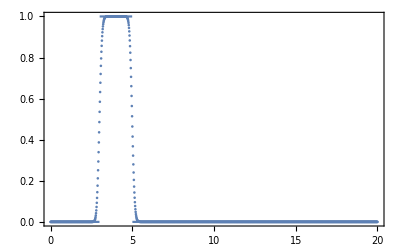

```mathematica
Show[{Plot[LAE`analyticSol[x],{x,0,20}],KT`system`solution`xui`t1[Last@LAE`solutions]//ListPlot}]
```

```mathematica
KT`system`solution`xui`t1[#][[1]]&/@LAE`solutions;
Abs[#[[All,2]]-(LAE`analyticSol/@#[[All,1]])]&/@%;
{Length[#],Norm[#,1]/Length[#],Norm[#,∞]/Length[#]}&/@%;
{%[[All,1]],%[[All,2]],Prepend[-Log@Ratios[%[[All,2]]]/Log@Ratios[%[[All,1]]],0],%[[All,3]],Prepend[-Log@Ratios[%[[All,3]]]/Log@Ratios[%[[All,1]]],0]}ᵀ;
TableForm[%,TableHeadings->{None,{"N","L^1-error","Rate","L^∞-error","Rate"}}]
```

N | L^1-error | Rate | L^∞-error | Rate
40 | 0.0534413 | 0 | 0.0108634 | 0
80 | 0.038911 | 0.457777 | 0.00555153 | 0.968515
160 | 0.0278629 | 0.481834 | 0.00287478 | 0.949432
320 | 0.0198243 | 0.491075 | 0.0014741 | 0.963614
640 | 0.0140613 | 0.495542 | 0.000750013 | 0.974852
1280 | 0.00995818 | 0.497772 | 0.000379584 | 0.982498

```mathematica
KT`system`solution`Δx[#]&/@LAE`solutions
```

{0.512821,0.253165,0.125786,0.0626959,0.0312989,0.0156372}

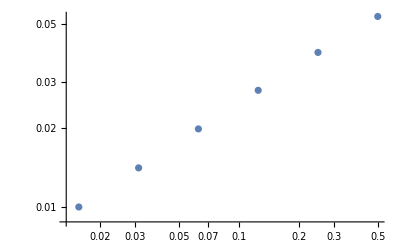

FittedModel[0.0748314 Δx^0.478632]

```mathematica
KT`system`solution`xui`t1[#][[1]]&/@LAE`solutions;
Abs[#[[All,2]]-(LAE`analyticSol/@#[[All,1]])]&/@%;
{20/Length[#],Norm[#,1]/Length[#]}&/@%;
%//ListLogLogPlot
NonlinearModelFit[%%,a Δx^b,{a,b},Δx]
```

Burgers’ Equation: Pre- and Post-shock Solutions (BE) [KTO2-0, Example 3]

∂_t u[t,x]+∂_x (u[t,x]^2/2)==0; [KTO2-0,eq. (6.5)]
u[0,x]==1/2+Sin[x]; [KTO2-0,eq. (6.6)]
u[t,x]==1/2+Sin[x-u[t,x] t], ∀ 0≤t<-1/Min[D[u[0,x],x]]=1 [https://en.wikipedia.org/wiki/Burgers%27_equation]

```mathematica
BE`pde=Sequence[{(#3[[1]])^2/2}&,{#3[[1]]}&,{0}&];
BE`ics=1/2+Sin[#]&;
BE`systems=Table[KT`system`generate[KT`O1][n,1][0.,2.*π][0.,2][BE`pde,BC`periodic][BE`ics][None],{n,{40,80,160,320,640,1280}}];
```

```mathematica
BE`solutions=Table[KT`system`solve[s][False],{s,BE`systems}];
```

```mathematica
BE`solution`analytic[t_/;0<=t<1,x_]:=u/.NSolve[1/2+Sin[x-u t]==u,u,Reals][[1]]
```

```mathematica
KT`system`solution`xui`t[#,0.5][[1]]&/@BE`solutions;
#[[All,2]]-(BE`solution`analytic[0.5,#]&/@#[[All,1]])&/@%;
{Length[#],Norm[#,1]/Length[#],Norm[#,∞]/Length[#]}&/@%;
{%[[All,1]],%[[All,2]],Prepend[-Log@Ratios[%[[All,2]]]/Log@Ratios[%[[All,1]]],0],%[[All,3]],Prepend[-Log@Ratios[%[[All,3]]]/Log@Ratios[%[[All,1]]],0]}ᵀ;
TableForm[%,TableHeadings->{None,{"N","L^1-error","Rate","L^∞-error","Rate"}}]
```

Burgers-Type Equation with Saturating Dissipation (BESD) [KTO2-0, Example 6, eq. (6.8)]

∂_t u[t,x]+∂_x (u[t,x]^2)==∂_x ((∂_x u)/(√(1+(∂_x u)^2))); [KTO2-0,eq. (1.3) with f(u)=u^2]
u[0,x]==Piecewise[{{1.2,X<0}},-1.2]; [KTO2-0,eq. (6.8)]

```mathematica
BESD`pde=Sequence[{#3[[1]]^2}&,{2#3[[1]]}&,{(#4[[1]])/(√(1+(#4[[1]])^2))}&];
BESD`ics=Piecewise[{{1.2,#<0}},-1.2]&;
BESD`system=KT`system`generate[KT`O1][400,1][-3.,+3.][0.,1.5][BESD`pde,BC`linearExtrapolation][BESD`ics][];
```

```mathematica
BESD`solution=KT`system`solve[BESD`system,PrecisionGoal->16][]
```

```mathematica
KT`system`solution`xui`t`Manipulate[BESD`solution,Mesh->All]
```

## O(N=1) Model in d=0

## Exact solution

```mathematica
ClearAll[Gϕ];Protect[ϕ2];
Gϕ[m_,n_:n]:=If[EvenQ[m],((m-1)!!)/(Times@@Table[(n+(2i-2)),{i,1,m/2}])ϕ2[m/2],0]
ClearAll[Γϕ];
Γϕ[m_,n_:n]:=Module[{mastereq,eq,Γ,ϕ,Z,i},
If[OddQ[m],Return[0]];
If[m==2,Return[1/Gϕ[2,n]]];

mastereq=Γ[ϕ]==Γ'[ϕ]ϕ-Log[Z[Γ'[ϕ]]/Z[0]];
eq=D[mastereq,{ϕ,m}]//.{Derivative[i_][Z][Γ'[ϕ]]/;OddQ[i]:>0,Derivative[i_][Γ][ϕ]/;OddQ[i]:>0,Derivative[i_][Z][0]/;EvenQ[i]:>Gϕ[i,n]*Z[0]}/.Derivative[i_][Γ][ϕ]->Γ[i];
Return[eq[[2]]/.Γ[2]->1/Gϕ[2,n]/.Γ[i_]:>Γϕ[i,n]//Expand]
]

ClearAll[Γm];
Γm[ϕ2f_Function][m_,n_]:=Module[{symbolic,ϕ2i},
If[OddQ[m],Return[0]];
symbolic=Γϕ[m,n];
ϕ2i=DeleteDuplicates[Cases[Level[symbolic,∞,Heads->True],ϕ2[_]]]/.ϕ2[i_]:>i;
ϕ2i=Table[ϕ2[i]->ϕ2f[i,n],{i,ϕ2i}];
symbolic/.ϕ2i
]
```

```mathematica
ClearAll[ϕ2Analytic]
ϕ2Analytic[Uφ_,pars___][assumptions___]:=Module[{int,m,n},
int=(2^m Integrate[ρ^((n-2)/2)ρ^m Exp[-Uφ[√(2ρ),pars]],{ρ,0,∞},Assumptions->Flatten[Join[{assumptions},{n>0,m>0}]]])/Integrate[ρ^((n-2)/2)Exp[-Uφ[√(2ρ),pars]],{ρ,0,∞},Assumptions->Flatten[Join[{assumptions},{n>0,m>0}]]];
Return[{mi,ni}↦Evaluate[int/.{m->mi,n->ni}]]
]
```

```mathematica
ClearAll[ϕ2Numeric]
ϕ2Numeric[Uφ_,pars___][opts_:{AccuracyGoal->10,PrecisionGoal->10}]:=With[{sopts=Evaluate[Sequence@@opts]},{m,n}↦(2^m NIntegrate[ρ^((n-2)/2)ρ^m Exp[-Uφ[√(2ρ),pars]],{ρ,0,∞},sopts])/NIntegrate[ρ^((n-2)/2)Exp[-Uφ[√(2ρ),pars]],{ρ,0,∞},sopts]]
```

Formulas

```mathematica
Table[Γ[m]->Γm[ϕ[#1,#2]&][m,n],{m,{0,2,4,6}}]
{1,n/ϕ[1,n],(3 n^2)/ϕ[1,n]^2,(60 n^3)/ϕ[1,n]^3};
%%[[All,2]]/%//Expand
{%%%[[All,1]],%%,%}ᵀ//.ϕ[m_,n_]:>Row[{"<",(ϕ^2)^m,">"}]//TableForm
```

{Γ[0]→0,Γ[2]→n/ϕ[1,n],Γ[4]→(3 n^2)/ϕ[1,n]^2-(3 n^3 ϕ[2,n])/((2+n) ϕ[1,n]^4),Γ[6]→(60 n^3)/ϕ[1,n]^3-(135 n^4 ϕ[2,n])/((2+n) ϕ[1,n]^5)+(90 n^5 ϕ[2,n]^2)/((2+n)^2 ϕ[1,n]^7)-(15 n^5 ϕ[3,n])/((2+n) (4+n) ϕ[1,n]^6)}

{0,1,1-(n ϕ[2,n])/((2+n) ϕ[1,n]^2),1-(9 n ϕ[2,n])/(4 (2+n) ϕ[1,n]^2)+(3 n^2 ϕ[2,n]^2)/(2 (2+n)^2 ϕ[1,n]^4)-(n^2 ϕ[3,n])/(4 (2+n) (4+n) ϕ[1,n]^3)}

Γ[0] | 1 | 0
Γ[2] | n/(<ϕ^2>) | 1
Γ[4] | (3 n^2)/((<ϕ^2>)^2) | 1-(n <ϕ^4>)/((2+n) (<ϕ^2>)^2)
Γ[6] | (60 n^3)/((<ϕ^2>)^3) | 1-(9 n <ϕ^4>)/(4 (2+n) (<ϕ^2>)^2)+(3 n^2 (<ϕ^4>)^2)/(2 (2+n)^2 (<ϕ^2>)^4)-(n^2 <ϕ^6>)/(4 (2+n) (4+n) (<ϕ^2>)^3)

## Numerical derivatives

Formulas

```mathematica
InterpolatingPolynomial[Table[{Δx i,u[i]},{i,-1,1}],x]//Simplify;
D[%,{x,1}]/.x->0/.u[j_]:>Subscript[f, i+j]//Simplify
%/.i->0/.Subscript[f, i_]/;i<0:>-Subscript[f, -i]//Simplify

InterpolatingPolynomial[Table[{Δx i,u[i]},{i,-2,2}],x]//Simplify;
D[%,{x,1}]/.x->0/.u[j_]:>Subscript[f, i+j]//Simplify
%/.i->0/.Subscript[f, i_]/;i<0:>-Subscript[f, -i]//Simplify
```

```mathematica
InterpolatingPolynomial[Table[{Δx i,u[i]},{i,-3,3}],x]//Simplify;
D[%,{x,1}]/.x->0/.u[j_]:>Subscript[f, i+j]//Simplify
%/.i->0/.Subscript[f, i_]/;i<0:>-Subscript[f, -i]//Simplify
```

```mathematica
InterpolatingPolynomial[Table[{Δx i,u[i]},{i,-2,2}],x]//Simplify;
D[%,{x,3}]/.x->0/.u[j_]:>Subscript[f, i+j]//Simplify
%/.i->0/.Subscript[f, i_]/;i<0:>-Subscript[f, -i]//Simplify

InterpolatingPolynomial[Table[{Δx i,u[i]},{i,-3,3}],x]//Simplify;
D[%,{x,3}]/.x->0/.u[j_]:>Subscript[f, i+j]//Simplify
%/.i->0/.Subscript[f, i_]/;i<0:>-Subscript[f, -i]//Simplify
```

```mathematica
InterpolatingPolynomial[Table[{Δx i,u[i]},{i,-3,3}],x]//Simplify;
D[%,{x,5}]/.x->0/.u[j_]:>Subscript[f, i+j]//Simplify
%/.i->0/.Subscript[f, i_]/;i<0:>-Subscript[f, -i]

InterpolatingPolynomial[Table[{Δx i,u[i]},{i,-4,4}],x]//Simplify;
D[%,{x,5}]/.x->0/.u[j_]:>Subscript[f, i+j]//Simplify
%/.i->0/.Subscript[f, i_]/;i<0:>-Subscript[f, -i]
```

### Implementation

```mathematica
Γ2OΔx2C[uxi_List]:=With[{Δx=uxi[[2,1]]-uxi[[1,1]],f1=uxi[[2,2]]},f1/Δx]
Γ2OΔx4C[uxi_List]:=With[{Δx=uxi[[2,1]]-uxi[[1,1]],f1=uxi[[2,2]],f2=uxi[[3,2]]},-(-8f1+f2)/(6Δx)]
Γ2OΔx6C[uxi_List]:=With[{Δx=uxi[[2,1]]-uxi[[1,1]],f1=uxi[[2,2]],f2=uxi[[3,2]],f3=uxi[[4,2]]},(45f1-9f2+f3)/(30Δx)]

Γ4OΔx2C[uxi_List]:=With[{Δx=uxi[[2,1]]-uxi[[1,1]],f1=uxi[[2,2]],f2=uxi[[3,2]]},(-2f1+f2)/(Δx^3)]
Γ4OΔx4C[uxi_List]:=With[{Δx=uxi[[2,1]]-uxi[[1,1]],f1=uxi[[2,2]],f2=uxi[[3,2]],f3=uxi[[4,2]]},-(13f1-8f2+f3)/(4 Δx^3)]

Γ6OΔx2C[uxi_List]:=With[{Δx=uxi[[2,1]]-uxi[[1,1]],f1=uxi[[2,2]],f2=uxi[[3,2]],f3=uxi[[4,2]]},(10f1-8f2+2f3)/(2 Δx^5)]
Γ6OΔx4C[uxi_List]:=With[{Δx=uxi[[2,1]]-uxi[[1,1]],f1=uxi[[2,2]],f2=uxi[[3,2]],f3=uxi[[4,2]],f4=uxi[[5,2]]},(58f1-52f2+18f3-2)/(6 Δx^5)]
```

```mathematica
ClearAll[Γn];
Γn[Γ_][sol_/;MatchQ[sol,KT`system`solution[___][___][___]],t_:"IR"]:=If[t==="IR",
Γ[KT`system`solution`xui`t1[sol][[1]]],
Γ[KT`system`solution`xui`t[sol,t][[1]]]
]
```

## ICs

```mathematica
ClearAll[PiecewiseMonomial];
PiecewiseMonomial[a_,c_,n_]:=Module[{l,f,y,df},
l=Length[n];
f[i_][x_]:=c[[i]](x-a[[1]])^n[[i]]+If[i>1,f[i-1][a[[i]]]-c[[i]](a[[i]]-a[[1]])^n[[i]],0];
df[i_][x_]:=D[f[i][y],y]/.y->x;
{Function[Evaluate[Piecewise[Table[{df[i][Slot[1]],a[[i]]≤Slot[1]<a[[i+1]]},{i,1,l-1}],df[l][Slot[1]]]]],
Function[Evaluate[Piecewise[Table[{f[i][Slot[1]],a[[i]]≤Slot[1]<a[[i+1]]},{i,1,l-1}],f[l][Slot[1]]]]]}
]
```

```mathematica
ClearAll[PiecewiseMonomialAnti];
PiecewiseMonomialAnti[a_,c_,n_]:=Module[{l,f,y,df,fi,Fi},
l=Length[n];
f[i_][x_]:=c[[i]](x-a[[1]])^n[[i]]+If[i>1,f[i-1][a[[i]]]-c[[i]](a[[i]]-a[[1]])^n[[i]],0];
df[i_][x_]:=D[f[i][y],y]/.y->x;
fi=Table[{df[i][Slot[1]],a[[i]]≤Slot[1]<a[[i+1]]},{i,1,l-1}];
fi=Join[{{-fi[[1,1]]/.Slot[1]->Abs[Slot[1]],-fi[[1,2,-1]]≤Slot[1]<0}},fi];
Fi=Table[{f[i][Slot[1]],a[[i]]≤Slot[1]<a[[i+1]]},{i,1,l-1}];
Fi=Join[{{Fi[[1,1]]/.Slot[1]->Abs[Slot[1]],-Fi[[1,2,-1]]≤Slot[1]<0}},Fi];

{Function[Evaluate[Piecewise[fi,df[l][Slot[1]]]//Simplify]],
Function[Evaluate[Piecewise[Fi,f[l][Slot[1]]]//Simplify]]}
]
```

```mathematica
ClearAll[PiecewisePolynomial];
PiecewisePolynomial[a_,c_,n_]:=Module[{l,f,y,df},
l=Length[n];
f[i_][x_]:=c[[i]](x-a[[i]])^n[[i]]+If[i>1,f[i-1][a[[i]]],0];
df[i_][x_]:=D[f[i][y],y]/.y->x;
{Function[Evaluate[Piecewise[Table[{df[i][Slot[1]],a[[i]]≤Slot[1]<a[[i+1]]},{i,1,l-1}],df[l][Slot[1]]]]],
Function[Evaluate[Piecewise[Table[{f[i][Slot[1]],a[[i]]≤Slot[1]<a[[i+1]]},{i,1,l-1}],f[l][Slot[1]]]]]}
]
```

### Scenario 1

```mathematica
ICS1=PiecewiseMonomialAnti[{0,2,3},{-1/2,-2,1/2},{2,0,2}];
```

### Scenario 2

```mathematica
ICS2={-#+1/(3!)#^3&,-1/2#^2+1/(4!)#^4&};
```

```mathematica
ICS2plus={#+1/(3!)#^3&,1/2#^2+1/(4!)#^4&};
```

### Scenario 3

```mathematica
ICS3={#-4/20#^3+1/(5!)#^5&,1/2#^2-1/20#^4+1/(6!)#^6&};
```

### Scenario 4

```mathematica
ICS4={Piecewise[{{-2#/(3(#^2)^(2/3)),#≤√8}},#]&,Piecewise[{{-(#^2)^(1/3),#≤√8}},1/2#^2-6]&};
```

## FRG

∂_t u[t,σ]-∂_σ (1/2(∂_t r_b[t])(n-1)/(r_b[t]+u[t,σ]/σ))-∂_σ (1/2(∂_t r_b[t])1/(r_b[t]+∂_σ u[t,σ]))=0,
∂_t u[t,σ]+∂_σ F[t,σ,u]=∂_σ Q[t,σ,u,∂_σ u],
F[t,σ,u]=-1/2(∂_t r_b[t])(n-1)/(r_b[t]+u[t,σ]/σ)=1/2(n-1)r_b[t]/(r_b[t]+u[t,σ]/σ),
(∂F[t,σ,u])/(∂u)=+1/2(∂_t r_b[t])((n-1)σ)/(r_b[t]σ+u[t,σ])^2=-1/2(n-1)(r_b[t]σ)/(r_b[t]σ+u[t,σ])^2,
Q[t,σ,u,∂_σ u]=Q[t,∂_σ u]=1/2(∂_t r_b[t])1/(r_b[t]+∂_σ u[t,σ])=-1/2 r_b[t]/(r_b[t]+∂_σ u[t,σ]),
where r_b[t]=Λ Exp[-t] and  ∂_t r_b[t]=-Λ Exp[-t]=-r_b[t].

```mathematica
ON0d`PDE`F={t,x,u,pars}↦With[{nπ=pars[[1]]-1,rb=pars[[2]]Exp[-t]},{0.5nπ((rb x)/(rb x+u[[1]]))}];
ON0d`PDE`dFdx={t,x,u,pars}↦With[{nπ=pars[[1]]-1,rb=pars[[2]]Exp[-t]},{-0.5nπ((rb x)/(rb x+u[[1]])^2)}];
ON0d`PDE`Q={t,x,u,dudx,pars}↦With[{rb=pars[[2]]Exp[-t]},{-0.5(rb/(rb+dudx[[1]]))}];
ON0d`PDE=Sequence[ON0d`PDE`F,ON0d`PDE`dFdx,ON0d`PDE`Q];
```

```mathematica
ON0d`PDE`BC=Function[{vin},Module[{v},
v=vin;
v[[All,1]]=-v[[All,5]];(* Subscript[u, -2] = -Subscript[u, 2] *)
v[[All,2]]=-v[[All,4]];(* Subscript[u, -1] = -Subscript[u, 1] *)
v[[All,3]]=0*v[[All,3]]; (* Subscript[u, 0] = 0 *)
v[[All,-2]]=2v[[All,-3]]-v[[All,-4]];(* Subscript[u, n] = 2 Subscript[u, n-1] - Subscript[u, n-2] [linear extrapolation]*)
v[[All,-1]]=3v[[All,-3]]-2v[[All,-4]];(* Subscript[u, n+1]= 3 Subscript[u, n-1] - 2Subscript[u, n-2] [linear extrapolation]*)
v
]];
```

### Entropy functionals

-∑_(i=0)^(n-1) (u_(i+1)-u_(i-1))^2/(2(1+δ_(i,0)+δ_(i,n-1))Δx)

```mathematica
CFunctional[y_:(y↦y^2)][sol_,t_]:=Module[{Δx,n,uiPadded,duidxCentral},
Δx=KT`system`solution`Δx[sol];
n=KT`system`solution`nx[sol];
uiPadded={ArrayPad[KT`system`solution`ui`t[sol,t],2]}//ON0d`PDE`BC//Flatten//Take[#,{2,-2}]&;
duidxCentral=((#[[3;;]]-#[[;;-3]]&@uiPadded))/(2Δx);
(-2*(y[#]&/@duidxCentral)*ArrayPad[ConstantArray[1,n-2],1,1/2]*Δx)//Total
]
```

```mathematica
CFunctionalExplicit[sol_,t_]:=Module[{n,Δx,ui,ui0},
n=KT`system`solution`nx[sol];
Δx=KT`system`solution`Δx[sol];
ui={ArrayPad[KT`system`solution`xui`t[sol,t][[1]][[All,2]],2]}//ON0d`PDE`BC//First;
ui0={ArrayPad[KT`system`solution`xui`t0[sol][[1]][[All,2]],2]}//ON0d`PDE`BC//First;
-1/(2Δx)Sum[((ui[[i+1+3]]-ui[[i-1+3]])^2-(ui0[[i+1+3]]-ui0[[i-1+3]])^2)/(1+KroneckerDelta[i,0]+KroneckerDelta[i,n-1]),{i,0,n-1}]
]
```

```mathematica
params={1(*n*),1.*10^6(*Λ*)};
systems=Table[KT`system`generate[KT`O2][n][0,10.][0.,60.][ON0d`PDE,ON0d`PDE`BC,params][ICS1][],{n,400,800,100}];
sols1even=Table[KT`system`solve[s,AccuracyGoal->10,PrecisionGoal->10][True,True,Range[0,60,1/4]],{s,systems}]
```

```mathematica
Table[{KT`system`solution`nx[s],With[{c0=CFunctional[][s,0],c1=CFunctional[][s,60]},Hold[Sequence][c0,c1,c1-c0]]},{s,sols1even}]//ReleaseHold
%//TableForm
ListPlot[%%[[All,{1,4}]]]
```

```mathematica
Table[{KT`system`solution`nx[s],With[{c0=CFunctional[][s,0],c1=CFunctional[][s,60]},Hold[Sequence][c0,c1,c1-c0]]},{s,sols}]//ReleaseHold
%//TableForm
ListPlot[%%[[All,{1,4}]]]
```

```mathematica
params={1(*n*),1.*10^12(*Λ*)};
systems=Table[KT`system`generate[KT`O2][n][0,10.][0.,60.][ON0d`PDE,ON0d`PDE`BC,params][ICS2][],{n,401,801,100}];
sols2=Table[KT`system`solve[s,AccuracyGoal->10,PrecisionGoal->10][True,True,Range[0,60,1/4]],{s,systems}]
```

```mathematica
Table[{KT`system`solution`nx[s],With[{c0=CFunctional[][s,0],c1=CFunctional[][s,60]},Hold[Sequence][c0,c1,c1-c0]]},{s,sols2}]//ReleaseHold
%//TableForm
ListPlot[%%[[All,{1,4}]]]
```

```mathematica
ϕ2Numeric[ICS3[[2]]][];
NumberForm[N[Simplify@FunctionExpand@Γm[%][2,10],37],37]
Γ2OΔx2C[KT`system`solution`xui`t1[sol][[1]]]/%-1//ScientificForm
```

```mathematica
CFunctional[][sol,0];
dat=Table[{t,CFunctional[][sol,t]-%},{t,0,56,1/4}];
Line[#]&/@({%[[;;-2]],%[[2;;]]}ᵀ);
Array[{CapForm["Round"],Thickness[.005],Blend[{GUCD`goetheBlau,GUCD`emoRot},( ( #- 1.)/( Length[%] - 1 ) )^(1/3)]}&,Length@%];
Show[MapThread[Graphics[Flatten[{#1,#2},1]]&,{%,%%}]];
Show[{ListPlot[{},PlotRange->{{0,56},{-200,2000}},PlotStyle->{{PointSize[.01],Gray}}],%},GridLines->Automatic,FrameLabel->{"t","C[∂_x u(t,x)]","u[t=0,σ]=σ-σ^3/5+σ^5/120, Λ=10^12, O(N=10), n=101"}]
```

### O(1) Tests

n=800;
params={1(*n*),1.*10^6(*Λ*)};
KT`system`generate[KT`O2][n][0,10.][0.,60.][ON0d`PDE,ON0d`PDE`BC,params][ICS1][];
SC1O1`sol=KT`system`solve[%,AccuracyGoal→10,PrecisionGoal→10][True,True]

params={1(*n*),1.*10^12(*Λ*)};
KT`system`generate[KT`O2][n][0,10.][0.,60.][ON0d`PDE,ON0d`PDE`BC,params][ICS2][];
SC2O1`sol=KT`system`solve[%,AccuracyGoal→10,PrecisionGoal→10][True,True]

KT`system`generate[KT`O2][n][0,10.][0.,60.][ON0d`PDE,ON0d`PDE`BC,params][ICS2plus][];
SC2pO1`sol=KT`system`solve[%,AccuracyGoal→10,PrecisionGoal→10][True,True]

params={1(*n*),1.*10^12(*Λ*)};
KT`system`generate[KT`O2][n][0,10.][0.,60.][ON0d`PDE,ON0d`PDE`BC,params][ICS3][];
SC3O1`sol=KT`system`solve[%,AccuracyGoal→10,PrecisionGoal→10][True,True]

params={1(*n*),1.*10^8(*Λ*)};
KT`system`generate[KT`O2][n][0,10.][0.,60.][ON0d`PDE,ON0d`PDE`BC,params][ICS4][];
SC4O1`sol=KT`system`solve[%,AccuracyGoal→10,PrecisionGoal→10][True,True]

KT`system`solution`tw[Symbol@#]&/@Names["SC*`sol"]/60//Total 
(*-> 8.112536035*)

SC1O1`sol//Export["SC1O1.mx.gz",#]&
SC2O1`sol//Export["SC2O1.mx.gz",#]&
SC2pO1`sol//Export["SC2pO1.mx.gz",#]&
SC3O1`sol//Export["SC3O1.mx.gz",#]&
SC4O1`sol//Export["SC4O1.mx.gz",#]&

```mathematica
SC1O1`sol=Import["SC1O1.mx.gz"]
SC2O1`sol=Import["SC2O1.mx.gz"]
SC2pO1`sol=Import["SC2pO1.mx.gz"]
SC3O1`sol=Import["SC3O1.mx.gz"]
SC4O1`sol=Import["SC4O1.mx.gz"]

KT`system`solution`tw[Symbol@#]&/@Names["SC*`sol"]/60//Total
```

#### Scenario 1 - O(N=1), Λ=10^6, n=800, x_1=10

SC1O1`params={1(*n*),1.*10^6(*Λ*)};
SC1O1`system=KT`system`generate[KT`O2][801][0,10.][0.,56.][ON0d`PDE,ON0d`PDE`BC,%][ICS1][]
SC1O1`sol=KT`system`solve[%,AccuracyGoal→10,PrecisionGoal→10][True,True]

```mathematica
SC1O1`solFlow=Table[KT`system`solution`xui`t[SC1O1`sol,t],{t,0,56,2}];
ListLinePlot[%[[All,1]],PlotRange->{{0,5},{-2.2,4.5}},PlotStyle->Evaluate[Array[{Thick,Blend[{GUCD`goetheBlau,GUCD`emoRot},( ( #- 1.)/( Length[%] - 1 ) )^(1/3)]}&,Length@%]]]
```

```mathematica
CFunctional[][SC1O1`sol,0];
CFunctional[][SC1O1`sol,56]-%
CFunctionalExplicit[SC1O1`sol,56]
```

```mathematica
ϕ2Analytic[ICS1[[2]]][];
N[Simplify@FunctionExpand@Γm[%][2,1],37]
ϕ2Numeric[ICS1[[2]]][];
NumberForm[N[Simplify@FunctionExpand@Γm[%][2,1],37],37]
Γ2OΔx2C[KT`system`solution`xui`t1[SC1O1`sol][[1]]]/%-1//ScientificForm
```

```mathematica
CFunctional[][SC1O1`sol,0];
dat=Table[{t,CFunctional[][SC1O1`sol,t]-%},{t,0,56,1/4}];
Line[#]&/@({%[[;;-2]],%[[2;;]]}ᵀ);
Array[{CapForm["Round"],Thickness[.005],Blend[{GUCD`goetheBlau,GUCD`emoRot},( ( #- 1.)/( Length[%] - 1 ) )^(1/3)]}&,Length@%];
Show[MapThread[Graphics[Flatten[{#1,#2},1]]&,{%,%%}]];
Show[{ListPlot[dat,PlotRange->{{0,56},{-100,1000}},PlotStyle->{{PointSize[.01],Gray}}],%}]
```

#### Scenario 2 - O(N=1), Λ=10^12, n=800, x_1=10

SC2O1`params={1(*n*),1.*10^12(*Λ*)};
SC2O1`system=KT`system`generate[KT`O2][801][0,10.][0.,56.][ON0d`PDE,ON0d`PDE`BC,%][ICS2][]
SC2O1`sol=KT`system`solve[%,AccuracyGoal→10,PrecisionGoal→10][True,True]

```mathematica
SC2O1`solFlow=Table[KT`system`solution`xui`t[SC2O1`sol,t],{t,0,56,2}];
ListLinePlot[%[[All,1]],PlotRange->{{0,5},{-2.2,4.5}},PlotStyle->Evaluate[Array[{Thick,Blend[{GUCD`goetheBlau,GUCD`emoRot},( ( #- 1.)/( Length[%] - 1 ) )^(1/3)]}&,Length@%]]]
```

```mathematica
CFunctional[][SC2O1`sol,0]
CFunctionalTest[SC2O1`sol,56]-%
```

```mathematica
ϕ2Analytic[ICS2[[2]]][];
N[Simplify@FunctionExpand@Γm[%][2,1],37]
ϕ2Numeric[ICS2[[2]]][];
NumberForm[N[Simplify@FunctionExpand@Γm[%][2,1],37],37]
Γ2OΔx2C[KT`system`solution`xui`t1[SC2O1`sol][[1]]]/%-1//ScientificForm
```

```mathematica
CFunctional[][SC2O1`sol,0];
dat=Table[{t,CFunctional[][SC2O1`sol,t]-%},{t,0,56,1/4}];
Line[#]&/@({%[[;;-2]],%[[2;;]]}ᵀ);
Array[{CapForm["Round"],Thickness[.005],Blend[{GUCD`goetheBlau,GUCD`emoRot},( ( #- 1.)/( Length[%] - 1 ) )^(1/3)]}&,Length@%];
Show[MapThread[Graphics[Flatten[{#1,#2},1]]&,{%,%%}]];
Show[{ListPlot[dat,PlotRange->{{0,56},{-10,50}},PlotStyle->{{PointSize[.01],Gray}}],%}]
```

#### Scenario 2 - O(N=1), Λ=10^12, n=800, x_1=10, positive mass

SC2pO1`params={1(*n*),1.*10^12(*Λ*)};
SC2pO1`system=KT`system`generate[KT`O2][801][0,10.][0.,56.][ON0d`PDE,ON0d`PDE`BC,%][ICS2plus][]
SC2pO1`sol=KT`system`solve[%,AccuracyGoal→10,PrecisionGoal→10][True,True]

```mathematica
SC2pO1`solFlow=Table[KT`system`solution`xui`t[SC2pO1`sol,t],{t,0,56,2}];
ListLinePlot[%[[All,1]],PlotRange->{{0,3},{-1,4.5}},PlotStyle->Evaluate[Array[{Thick,Blend[{GUCD`goetheBlau,GUCD`emoRot},( ( #- 1.)/( Length[%] - 1 ) )^(1/3)]}&,Length@%]]]
```

```mathematica
CFunctional[][SC2pO1`sol,0]
CFunctionalTest[SC2pO1`sol,56]-%
```

```mathematica
ϕ2Analytic[ICS2plus[[2]]][];
N[Simplify@FunctionExpand@Γm[%][2,1],37]
ϕ2Numeric[ICS2plus[[2]]][];
NumberForm[N[Simplify@FunctionExpand@Γm[%][2,1],37],37]
Γ2OΔx2C[KT`system`solution`xui`t1[SC2pO1`sol][[1]]]/%-1//ScientificForm
```

```mathematica
CFunctional[][SC2pO1`sol,0];
dat=Table[{t,CFunctional[][SC2pO1`sol,t]-%},{t,0,56,1/4}];
Line[#]&/@({%[[;;-2]],%[[2;;]]}ᵀ);
Array[{CapForm["Round"],Thickness[.005],Blend[{GUCD`goetheBlau,GUCD`emoRot},( ( #- 1.)/( Length[%] - 1 ) )^(1/3)]}&,Length@%];
Show[MapThread[Graphics[Flatten[{#1,#2},1]]&,{%,%%}]];
Show[{ListPlot[dat,PlotRange->{{0,56},{-10,50}},PlotStyle->{{PointSize[.01],Gray}}],%}]
```

#### Scenario 3 - O(N=1), Λ=10^12, n=800, x_1=10

SC3O1`params={1(*n*),1.*10^12(*Λ*)};
SC3O1`system=KT`system`generate[KT`O2][801][0,10.][0.,56.][ON0d`PDE,ON0d`PDE`BC,%][ICS3][]
SC3O1`sol=KT`system`solve[%,AccuracyGoal→10,PrecisionGoal→10][True,True]

```mathematica
SC3O1`solFlow=Table[KT`system`solution`xui`t[SC3O1`sol,t],{t,0,56,2}];
ListLinePlot[%[[All,1]],PlotRange->{{0,5},{-2.2,4.5}},PlotStyle->Evaluate[Array[{Thick,Blend[{GUCD`goetheBlau,GUCD`emoRot},( ( #- 1.)/( Length[%] - 1 ) )^(1/3)]}&,Length@%]]]
```

```mathematica
CFunctional[][SC3O1`sol,0]
CFunctionalTest[SC3O1`sol,56]-%
```

```mathematica
ϕ2Analytic[ICS3[[2]]][];
N[Simplify@FunctionExpand@Γm[%][2,1],37]
ϕ2Numeric[ICS3[[2]]][];
NumberForm[N[Simplify@FunctionExpand@Γm[%][2,1],37],37]
Γ2OΔx2C[KT`system`solution`xui`t1[SC3O1`sol][[1]]]/%-1//ScientificForm
```

```mathematica
CFunctional[][SC3O1`sol,0];
dat=Table[{t,CFunctional[][SC3O1`sol,t]-%},{t,0,56,1/4}];
Line[#]&/@({%[[;;-2]],%[[2;;]]}ᵀ);
Array[{CapForm["Round"],Thickness[.005],Blend[{GUCD`goetheBlau,GUCD`emoRot},( ( #- 1.)/( Length[%] - 1 ) )^(1/3)]}&,Length@%];
Show[MapThread[Graphics[Flatten[{#1,#2},1]]&,{%,%%}]];
Show[{ListPlot[dat,PlotRange->{{0,56},{-10,500}},PlotStyle->{{PointSize[.01],Gray}}],%}]
```

#### Scenario 4 - O(N=1), Λ=10^8, n=800, x_1=10

SC4O1`params={1(*n*),1.*10^8(*Λ*)};
SC4O1`system=KT`system`generate[KT`O2][801][0,10.][0.,56.][ON0d`PDE,ON0d`PDE`BC,%][ICS4][]
SC4O1`sol=KT`system`solve[%,AccuracyGoal→10,PrecisionGoal→10][True,True]

```mathematica
SC4O1`solFlow=Table[KT`system`solution`xui`t[SC4O1`sol,t],{t,0,56,2}];
ListLinePlot[%[[All,1]],PlotRange->{{0,5},{-2.2,4.5}},PlotStyle->Evaluate[Array[{Thick,Blend[{GUCD`goetheBlau,GUCD`emoRot},( ( #- 1.)/( Length[%] - 1 ) )^(1/3)]}&,Length@%]]]
```

```mathematica
CFunctional[][SC4O1`sol,0]
CFunctionalTest[SC4O1`sol,56]-%
```

```mathematica
ϕ2Analytic[ICS4[[2]]][];
N[Simplify@FunctionExpand@Γm[%][2,1],37]
ϕ2Numeric[ICS4[[2]]][];
NumberForm[N[Simplify@FunctionExpand@Γm[%][2,1],37],37]
Γ2OΔx2C[KT`system`solution`xui`t1[SC4O1`sol][[1]]]/%-1//ScientificForm
```

```mathematica
CFunctional[][SC4O1`sol,0];
dat=Table[{t,CFunctional[][SC4O1`sol,t]-%},{t,0,56,1/4}];
Line[#]&/@({%[[;;-2]],%[[2;;]]}ᵀ);
Array[{CapForm["Round"],Thickness[.005],Blend[{GUCD`goetheBlau,GUCD`emoRot},( ( #- 1.)/( Length[%] - 1 ) )^(1/3)]}&,Length@%];
Show[MapThread[Graphics[Flatten[{#1,#2},1]]&,{%,%%}]];
Show[{ListPlot[dat,PlotRange->{{0,56},{-100,3000}},PlotStyle->{{PointSize[.01],Gray}}],%}]
```

```mathematica
dat//Interpolation;
D[%[x],x]
Plot[%,{x,1,50},PlotRange->All]
```

### O(N) Tests

```mathematica
params=Table[{n(*n*),1.*10^6(*Λ*)},{n,1,10}];
systems=Table[KT`system`generate[KT`O2][101][0,10.][0.,56.][ON0d`PDE,ON0d`PDE`BC,p][ICS1][],{p,params}];
sols=Table[KT`system`solve[s,AccuracyGoal->10,PrecisionGoal->10][True,True,Range[0,56,1/4]],{s,systems}];
```

```mathematica
dats=Table[Table[{t,CFunctional[][s,t]-CFunctional[][s,0]},{t,0,56,1/4}],{s,sols}];
ListLinePlot[dats,PlotLegends->Placed[Table[Row[{"N=",n}],{n,1,10}],{Left,Top}],GridLines->{{},{0}},FrameLabel->{"t","C-fkt"},PlotLabel->"Scenario 1"]
```

```mathematica
params=Table[{n(*n*),1.*10^12(*Λ*)},{n,1,10}];
systems=Table[KT`system`generate[KT`O2][101][0,10.][0.,56.][ON0d`PDE,ON0d`PDE`BC,p][ICS2][],{p,params}];
sols=Table[KT`system`solve[s,AccuracyGoal->10,PrecisionGoal->10][True,True,Range[0,56,1/4]],{s,systems}];
```

```mathematica
dats=Table[Table[{t,CFunctional[][s,t]-CFunctional[][s,0]},{t,0,56,1/4}],{s,sols}];
ListLinePlot[dats,PlotLegends->Placed[Table[Row[{"N=",n}],{n,1,10}],{Left,Top}],GridLines->{{},{0}},FrameLabel->{"t","C-fkt"},PlotLabel->"Scenario 2 (N_crit=8)"]
((#[[All,2]]//Sort//First)<0)&/@dats//FirstPosition[#,True]&//First
```

```mathematica
params=Table[{n(*n*),1.*10^12(*Λ*)},{n,1,10}];
systems=Table[KT`system`generate[KT`O2][101][0,10.][0.,56.][ON0d`PDE,ON0d`PDE`BC,p][ICS2plus][],{p,params}];
sols=Table[KT`system`solve[s,AccuracyGoal->10,PrecisionGoal->10][True,True,Range[0,56,1/4]],{s,systems}];
```

```mathematica
dats=Table[Table[{t,CFunctional[][s,t]-CFunctional[][s,0]},{t,0,56,1/4}],{s,sols}];
ListLinePlot[dats,PlotLegends->Placed[Table[Row[{"N=",n}],{n,1,10}],{Left,Top}],GridLines->{{},{0}},FrameLabel->{"t","C-fkt"},PlotLabel->"Scenario 2 plus (N_crit=7)"]
((#[[All,2]]//Sort//First)<0)&/@dats//FirstPosition[#,True]&//First
```

```mathematica
params=Table[{n(*n*),1.*10^12(*Λ*)},{n,1,10}];
systems=Table[KT`system`generate[KT`O2][101][0,10.][0.,56.][ON0d`PDE,ON0d`PDE`BC,p][ICS3][],{p,params}];
sols=Table[KT`system`solve[s,AccuracyGoal->10,PrecisionGoal->10][True,True,Range[0,56,1/4]],{s,systems}];
```

```mathematica
dats=Table[Table[{t,CFunctional[][s,t]-CFunctional[][s,0]},{t,0,56,1/4}],{s,sols}];
ListLinePlot[dats,PlotLegends->Placed[Table[Row[{"N=",n}],{n,1,10}],{Left,Top}],GridLines->{{},{0}},FrameLabel->{"t","C-fkt"},PlotLabel->"Scenario 3 (N_crit=7)"]
((#[[All,2]]//Sort//First)<0)&/@dats//FirstPosition[#,True]&//First
```

```mathematica
params=Table[{n(*n*),1.*10^12(*Λ*)},{n,1,10}];
systems=Table[KT`system`generate[KT`O2][101][0,10.][0.,56.][ON0d`PDE,ON0d`PDE`BC,p][ICS4][],{p,params}];
sols=Table[KT`system`solve[s,AccuracyGoal->10,PrecisionGoal->10][True,True,Range[0,56,1/4]],{s,systems}];
```

```mathematica
dats=Table[Table[{t,CFunctional[][s,t]-CFunctional[][s,0]},{t,0,56,1/4}],{s,sols}];
ListLinePlot[dats,PlotLegends->Placed[Table[Row[{"N=",n}],{n,1,10}],{Left,Top}],GridLines->{{},{0}},FrameLabel->{"t","C-fkt"},PlotLabel->"Scenario 4"]
((#[[All,2]]//Sort//First)<0)&/@dats//FirstPosition[#,True]&//First
```